```mathematica
F[x_]:=1/2 ⅈ (PolyLog[2,-ⅈ ⅇ^x]-PolyLog[2,ⅈ ⅇ^x])
```

```mathematica
G3[a_,b_]:=F[a-b]+F[b-a]-π/2(a+b);
```

```mathematica
EnergySetup[n_,FacesCW_]:=Module[{i,rhoV,rhoF,include,LineFaces,f,Faces,NM,nonlinefaces,radii,RADII},
Faces=Sort/@FacesCW;
f=Length[Faces];
LineFaces={};rhoV=Table[Subscript[rV, i],{i,1,n-2}];rhoF=Table[Subscript[rF, i],{i,1,f-2}];
include = {};
nonlinefaces={};
For[i=1,i≤f,i++,
If[!(Faces[[i,-2]]==n-1&&Faces[[i,-1]]==n),
(* then *) AppendTo[include,i];AppendTo[nonlinefaces,FacesCW[[i]]],
(* else *) AppendTo[LineFaces,i]]];

NM=NMinimize[{∑_(k=1)^(f-2) ∑_(i=1)^Length[Faces[[include[[k]]]]] If[Faces[[include[[k]],i]]<n-1,G3[Subscript[rV, Faces[[include[[k]],i]]],Subscript[rF, k]],0]+∑_(i=1)^(n-2) Subscript[rV, i] π If[MemberQ[Flatten@Table[Faces[[LineFaces[[m]]]],{m,1,2}],i],(* then *) 1,(* else *) 2]+∑_(j=1)^(f-2) Subscript[rF, j] π If[MemberQ[Faces[[include[[j]]]],n-1]||MemberQ[Faces[[include[[j]]]],n],(* then *) 1,(* else *) 2],
∑_(i=1)^(n-2) Subscript[rV, i]+∑_(j=1)^(f-2) Subscript[rF, j]==0},Join[rhoV,rhoF]];
RADII=Exp[Re[Join[rhoV,rhoF]/.(NM[[2]])]];
RADII/=RADII[[1]];
radii=<||>;
For[i=1,i≤n-2,i++,
radii[i]=RADII[[i]]
];
For[i=1,i≤Length[nonlinefaces],i++,
radii[nonlinefaces[[i]]]=RADII[[n-2+i]]
];
{radii,LineFaces}
];
```

```mathematica
Boundary[n_,FacesCW_,LineFaces_,radii_,ϵ_:0]:=Module[{i,j,faces,vertices,lastvisited,d,h,H,breaker,unvisited,f,endcircle,ComputeEndcircle,ComputeEndcircle2,delete},
unvisited =FacesCW;(*Keeps track of the faces we haven't visited*)
f=Length[FacesCW];

faces=<||>; (* centers of face circles (or normals, for lines) *)
For[i=1,i≤f,i++,faces[FacesCW[[i]]]={-∞,-∞}];
vertices=<||>; (* centers of vertex circles (or normals, for lines) *)
For[i=1,i≤n-2,i++,vertices[i]={-∞,-∞}];
(* Radii is an assoc from v->rad and facelist->rad *)

(*Vertex circles going vertically upwards along first FaceLine*)
h=0; (* height along the left line *)
For[i=1,i≤Length[FacesCW[[LineFaces[[1]]]]]-2(*Number of vertex circles that lie along first LineFace*),i++,
vertices[FacesCW[[LineFaces[[1]],i]]]={0,h+radii[FacesCW[[LineFaces[[1]],i]]]};(*Set the center of this vertex circle*)
h+=2radii[[FacesCW[[LineFaces[[1]],i]]]]];(*Keeps track of our cumulative height as we climb up the first FaceLine*)

unvisited=Delete[unvisited,Position[unvisited,FacesCW[[LineFaces[[1]]]]]];

d=0;(*Horizontal distance*)

ComputeEndcircle[prev_,face_]:=
(*Returns which vertex circle we calculated last based on previous vertex circle and face*)
If[face[[Mod[Position[face,n-1][[1,1]]-2,Length[face]]+1]]==prev,
(*then*)face[[Mod[Position[face,n-1][[1,1]],Length[face]]+1]],
(*else*) face[[Mod[Position[face,n-1][[1,1]]-2,Length[face]]+1]]];

endcircle=ComputeEndcircle[n,FacesCW[[LineFaces[[1]]]]];(*Previous vertex circle is bottom line, face is first FaceLine*)

(*Face circles going horizontally across upper vertex line*)
breaker=True;
For[j=1,j≤f ,j++,
For[i=1,i≤Length[unvisited],i++,
If[MemberQ[unvisited[[i]],n-1], (*determine if this face-circle contains n-1, so it is on the upper vertex line*)
If[MemberQ[unvisited[[i]],ComputeEndcircle[endcircle,unvisited[[i]]]],
(*determine if this face-circle also contains the vertex right before n-1 to ensure we are going horizontally across in the right order*)
If[unvisited[[i]]==FacesCW[[LineFaces[[2]]]],
(* If we've reached the second faceline, then do nothing--find the other face circle containing endcircle*)
,
(* else if the face circle is not a line*)
faces[unvisited[[i]]]={d+radii[unvisited[[i]]],h}; (*Set the center of this face circle*)
d+=2radii[unvisited[[i]]]; (* update how far along the top line we are *)
endcircle=ComputeEndcircle[endcircle,unvisited[[i]]];(*Update endcircle*)
unvisited=Delete[unvisited,i];] (* remove that face from the unvisited list *)
]
]
]
];
(*Vertex circles along the second FaceLine, climbing vertically upwards*)
h=0;
For[i=1,i≤Length[FacesCW[[LineFaces[[2]]]]]-2,i++,
vertices[FacesCW[[LineFaces[[2]],i]]]={d,h+radii[FacesCW[[LineFaces[[2]],i]]]};h+=2radii[[FacesCW[[LineFaces[[2]],i]]]]];
H=h;
h=0;(*Reset height*)

ComputeEndcircle2[prev_,face_]:=
If[face[[Mod[Position[face,n][[1,1]]-2,Length[face]]+1]]==prev,
(*then*)face[[Mod[Position[face,n][[1,1]],Length[face]]+1]],
(*else*) face[[Mod[Position[face,n][[1,1]]-2,Length[face]]+1]]];

endcircle=ComputeEndcircle2[n-1,FacesCW[[LineFaces[[1]]]]];
(*Face circles along lower vertex line, moving horizontally from origin to second FaceLine*)
d=0;(*Reset distance*)
breaker=True;
For[j=1,j≤f,j++,
For[i=1,i≤Length[unvisited],i++,
If[MemberQ[unvisited[[i]],n], (* determine if this face-circle contains n *)
If[MemberQ[unvisited[[i]],endcircle(* ComputeEndcircle2[endcircle,unvisited[[i]]] *)],(* determine if this face-cirlce also contains the vertex right before n *)
If[unvisited[[i]]==FacesCW[[LineFaces[[2]]]],
(* If we've reached the second faceline, then do nothing*)
,
(* else *)
faces[unvisited[[i]]]={d+radii[unvisited[[i]]],h}; (* then we'll make this face's center be where we know it is *)
d+=2radii[unvisited[[i]]]; (* update how far along the bottom line we are *)
endcircle=ComputeEndcircle2[endcircle,unvisited[[i]]];
unvisited=Delete[unvisited,i];] (* remove that face from the unvisited list *)
]
]
]
];
(*Set the normals of the vertex lines and face lines*)
faces[FacesCW[[LineFaces[[2]]]]]={1,0};
faces[FacesCW[[LineFaces[[1]]]]]={-1,0};
vertices[n]={0,-1};
vertices[n-1]={0,1};

If[ThrowOrderError[faces,vertices,radii,d,H,n,FacesCW[[LineFaces]],0],
faces[FacesCW[[LineFaces[[1]]]]]*=-1;
faces[FacesCW[[LineFaces[[2]]]]]*=-1;
For[i=1,i≤n,i++,
If[i==n-1||i==n,
,
If[Abs[vertices[i][[1]]-d]≤ϵ,
vertices[i]={0,vertices[i][[2]]},
If[Abs[vertices[i][[1]]-0]≤ϵ,
vertices[i]={d,vertices[i][[2]]}]];
]]];

(*Return the assoc's of the faces to their centers and vertices to their centers*)
{vertices,faces,d,H}
];
```

```mathematica
FindRest[{x_,y_},r_,face_,vertices_,radii_,lines_]:=(* face is all the vertices that the face intersects *)
(*{x_,y_},r: known center of opposite kind and its radius
face: all the circles of its kind that pass thru that opposite known circle
vertices: all the circles of its kind that are tangent to the one we'e looking for*)
Module[{verts=vertices,i,j,ϕ,θ,ω,face2=face,b,b2=True},

If[verts[face2[[1]]]=={-∞,-∞}||MemberQ[lines,face2[[1]]],
For[i=2,i≤Length[face2]&&b2,i++,
If[verts[face2[[i]]]≠{-∞,-∞}&&!MemberQ[lines,face2[[i]]],
face2=Join[face2[[i;;]],face2[[;;i-1]]];
b2=False;
]]];

b=True;
For[i=2,i≤Length[face2]&&b,i++,
If[MemberQ[lines,face2[[i]]],
AppendTo[face2,face2[[1]]];
For[j=Length[face2]-1,j>i,j--,
If[verts[face2[[j]]]=={-∞,-∞},
ϕ=ArcTan[verts[face2[[j+1]]][[1]]-x,verts[face2[[j+1]]][[2]]-y];
θ=ArcTan[radii[face2[[j+1]]]/r];(* j+1 refers to previously computed / known *)
ω=ArcTan[radii[face2[[j]]]/r];
verts[face2[[j]]]={x+√(r^2+radii[face2[[j]]]^2)Cos[ϕ-θ-ω],y+√(r^2+radii[face2[[j]]]^2)Sin[ϕ-θ-ω]}
]
];b=False;Break,
If[verts[face2[[i]]]=={-∞,-∞},
ϕ=ArcTan[verts[face2[[i-1]]][[1]]-x,verts[face2[[i-1]]][[2]]-y];
θ=ArcTan[radii[face2[[i-1]]]/r];(* i-1 refers to previously computed / known *)
ω=ArcTan[radii[face2[[i]]]/r];
verts[face2[[i]]]={x+√(r^2+radii[face2[[i]]]^2)Cos[ϕ+θ+ω],y+√(r^2+radii[face2[[i]]]^2)Sin[ϕ+θ+ω]}];
];];
verts
];
```

```mathematica
Cull[assoc_]:=Module[{vis={},unv={},i},For[i=1,i≤Length[Keys[assoc]],i++,If[assoc[Keys[assoc][[i]]]=={-∞,-∞},AppendTo[unv,Keys[assoc][[i]]],AppendTo[vis,Keys[assoc][[i]]]]];{vis,unv}]
```

```mathematica
Interior[n_,FacesCW_,LineFaces_,radii_,vertices_,faces_,d_,h_]:=
Module[{Vunv={},Funv={},Vvis={},Fvis={},i,j,f,verts=vertices,verts2,fcs=faces,fcs2,fi,vi,x,y,k,b},
f=Length[FacesCW];
For[i=1,i≤n,i++,
If[vertices[i]=={-∞,-∞},AppendTo[Vunv,i],AppendTo[Vvis,i]]];
For[i=1,i≤f,i++,
If[faces[FacesCW[[i]]]=={-∞,-∞},AppendTo[Funv,FacesCW[[i]]],AppendTo[Fvis,FacesCW[[i]]]]];

For[j=1,j≤n+Length[FacesCW]&&(Length[Vunv]+Length[Funv]>0),j++,

For[i=1,i≤Length[Fvis],i++,(* for a known face circle *)
If[Length[Intersection[Vvis,Fvis[[i]]]]*Length[Intersection[Vunv,Fvis[[i]]]]>0,
fi=Fvis[[i]];
{x,y}=fcs[fi];
verts2=FindRest[{x,y},radii[fi],fi,verts,radii,{n-1,n}];
If[ThrowOrderError[fcs,verts2,radii,d,h,n,{FacesCW[[LineFaces[[1]]]],FacesCW[[LineFaces[[2]]]]},0],verts=FindRest[{x,y},radii[fi],Reverse[fi],verts,radii,{n-1,n}],
verts=verts2];
];
{Vvis,Vunv}=Cull[verts];
];

For[i=1,i≤Length[Vvis],i++, (* for a known vertex circle *)
If[b=False;
For[k=1,k≤Length[Fvis],k++,b=b||If[MemberQ[Fvis[[k]],Vvis[[i]]],True,False]];b,
If[b=False;For[k=1,k≤Length[Funv],k++,b=b||If[MemberQ[Funv[[k]],Vvis[[i]]],True,False]];b,
(* then *)
vi=Vvis[[i]];
{x,y}=verts[vi];
fcs2=FindRest[{x,y},radii[vi],FacesList[vi,FacesCW],fcs,radii,FacesCW[[LineFaces]]];
If[ThrowOrderError[fcs2,verts,radii,d,h,n,FacesCW[[LineFaces]],0],
fcs=FindRest[{x,y},radii[vi],
Reverse[FacesList[vi,FacesCW]],fcs,radii,FacesCW[[LineFaces]]],
fcs=fcs2];
];
{Fvis,Funv}=Cull[fcs];
]
];
];
{verts,fcs}
];
```

```mathematica
ThrowOrderError[fcs2_,verts_,radii_,d_,h_,n_,fls_,ϵ_](* fcs2 is proposed fcs association. fls is facelines *):=
Module[{i,j,b,b2,K},
K={};
For[i=1,i≤Length[Keys[fcs2]],i++,
If[!MemberQ[fls,Keys[fcs2][[i]]],AppendTo[K,Keys[fcs2][[i]]]]
];

b=False; (* "breaker" *)
For[i=1,i≤Length[K]&&!b,i++,
If[b2=False;
-∞<fcs2[K[[i]]][[1]]<0
||-∞<fcs2[K[[i]]][[2]]<0
||fcs2[K[[i]]][[1]]>d
||fcs2[K[[i]]][[2]]>h
||(For[j=1,j≤Length[K[[i]]],j++,
If[K[[i,j]]≠n-1&&K[[i,j]]≠n&&verts[K[[i,j]]]≠{-∞,-∞}&&fcs2[K[[i]]]≠{-∞,-∞},
If[EuclideanDistance[verts[K[[i,j]]],fcs2[K[[i]]]]≥(1-ϵ)(radii[K[[i,j]]]+radii[K[[i]]]),b2=True;Break]]];b2),
b=True,

For[j=1,j≤Length[K]&&!b,j++,
If[i≠j&&fcs2[K[[i]]]≠{-∞,-∞}&&fcs2[K[[j]]]≠{-∞,-∞}&&
EuclideanDistance[fcs2[K[[i]]],fcs2[K[[j]]]]<(1+ϵ)(radii[fcs2[K[[i]]]]+radii[fcs2[K[[j]]]])
,(* then, bad *) b=True]]];
];


For[i=1,i≤Length[fls[[1]]]&&!b,i++,
If[verts[fls[[1,i]]][[1]]≠d/2+fcs2[fls[[1]]][[1]] d/2&&fls[[1,i]]<n-1,b=True]
];
For[i=1,i≤Length[fls[[2]]]&&!b,i++,
If[verts[fls[[2,i]]][[1]]≠d/2+fcs2[fls[[2]]][[1]] d/2&&fls[[2,i]]<n-1,b=True]
];

b
];
```

```mathematica
FacesList[v_,Faces_]:=
Module[{ContainV={},i,L=2,p=3,temp},
For[i=1,i≤Length[Faces],i++,
If[MemberQ[Faces[[i]],v],AppendTo[ContainV,Faces[[i]]]]];
While[L<Length[ContainV],
While[p≤Length[ContainV],
If[Length[Intersection[ContainV[[L-1]],ContainV[[p]]]]==2,
temp=ContainV[[p]];ContainV[[p]]=ContainV[[L]];ContainV[[L]]=temp;p=1+Length[ContainV],
p++]
];
L++;
p=L+1;
];
ContainV];
```

```mathematica
Q=({{0, 1/2, 0, 0}, {1/2, 0, 0, 0}, {0, 0, -1, 0}, {0, 0, 0, -1}});
```

```mathematica
InvCoords[z_,r_,d_:0]:=If[r==∞,{2d,0,z},{Norm[z]^2/r-r,1/r,z/r}];
```

```mathematica
Gram[SC_]:=SC.Q.Transpose[SC];
SuperCluster[vertices_,faces_,radii_,fls_,d_,h_,n_]:=
Module[{sc={},i},
For[i=1,i≤n-2,i++,AppendTo[sc,Flatten[InvCoords[vertices[i],radii[i]]]]];
AppendTo[sc,Flatten[InvCoords[vertices[n-1],∞,h/2+vertices[n-1][[2]] h/2]]];
AppendTo[sc,Flatten[InvCoords[vertices[n],∞,h/2+vertices[n][[2]] h/2]]];
For[i=1,i≤Length[Keys[faces]],i++,
If[!MemberQ[fls,Keys[faces][[i]]],
AppendTo[sc,Flatten[InvCoords[faces[Keys[faces][[i]]],radii[Keys[faces][[i]]]]]]
]];
AppendTo[sc,Flatten[InvCoords[faces[fls[[1]]],∞,d/2+faces[fls[[1]]][[1]] d/2]]];
AppendTo[sc,Flatten[InvCoords[faces[fls[[2]]],∞,d/2+faces[fls[[2]]][[1]] d/2]]];
sc
];
```

```mathematica
DrawCircle[{bhat_,b_,bx_,by_}]:=If[Abs[b]≥ .01,Circle[{bx,by}/b,1/b],InfiniteLine[{bx,by}bhat/2,{-by,bx}]];
```

```mathematica
Packing[n_,FacesCW_,ϵ_:0]:=
Module[{radii,LineFaces,vertices,faces,d,h},
{radii,LineFaces}=EnergySetup[n,FacesCW];
{vertices,faces,d,h}=Boundary[n,FacesCW,LineFaces,radii,ϵ];
{vertices,faces}=Interior[n,FacesCW,LineFaces,radii,vertices,faces,d,h];
{vertices,faces,radii,d,h,LineFaces}];
```

```mathematica
Render[radii_,fcs_,verts_,fls_,n_,d_,h_]:=Graphics[{Blue,Thick,
Table[If[i==n-1,Line[{{-Max[Values[radii]],h},{d+Max[Values[radii]],h}}],If[i==n,Line[{{-Max[Values[radii]],0},{d+Max[Values[radii]],0}}],
Circle[verts[Keys[verts][[i]]],radii[Keys[verts][[i]]]]]],{i,1,n}],
Red,Dashed,
Table[If[Keys[fcs][[i]]==fls[[1]],Line[{{0,-Max[Values[radii]]},{0,h+Max[Values[radii]]}}],
If[Keys[fcs][[i]]==fls[[2]],Line[{{d,-Max[Values[radii]]},{d,h+Max[Values[radii]]}}],
Circle[fcs[Keys[fcs][[i]]],radii[Keys[fcs][[i]]]]]],{i,1,Length[Keys[fcs]]}]
}];
```

```mathematica
SendToInt[ϵ_:0][y_]:=With[{x=Simplify[y]},If[Abs[x-Floor[x]]≤ϵ ,Floor[x],
If[Abs[x-Ceiling[x]]≤ ϵ ,Ceiling[x],x],x]];
```

```mathematica
R[vhat_]:=IdentityMatrix[4]+2Q.Transpose[{vhat}].{vhat}
BMat[n_]:=Table[b[i,j],{i,1,n},{j,1,n}];
```

```mathematica
Bend4[V_,n_][i_]:=With[{B=Bend3[V,n,Integers][i]},
If[Length[B]>0,
{B,"integral"},
{Bend3[V,n,Reals][i],"nonintegral"}
]
]

Bend3[V_,n_,RING_:Integers][i_]:=Module[{sol,assignments,rest,j,l,others1,others2,co,cl},
cl = V[[;;n]];
co = V[[n+1;;]];
sol=Solve[BMat[n].cl==cl.R[co⟦i⟧],RING];
If[sol=={},Null,
sol=sol⟦1⟧;
assignments=Association[sol];
rest=Complement[Flatten[BMat[n]],Keys[assignments]];
l=Length[rest];
If[l==0,MatrixForm[Simplify[BMat[n]/.assignments]],
others1=Solve[rest==Table[0,{j,1,l}]]⟦1⟧;
others2=<||>;
For[j=1,j≤l,j++,others2[rest⟦j⟧]=Subscript[a, j]];
others2=Normal[others2];
MatrixForm[Simplify[(BMat[n]/.(assignments/.others1))/.others1]]
]
]
]
```

```mathematica
Everything[n_,FacesCW_,ϵ_:0,steps_,sizemax_:∞]:=Module[{vertices,faces,f=Length[FacesCW],radii,d,h,LineFaces,Vnye,Vout,bends={}},
{vertices,faces,radii,d,h,LineFaces}=Packing[n,FacesCW,ϵ];
Vnye=SendToInt[ϵ]//@SuperCluster[vertices,faces,radii,FacesCW[[LineFaces]],d,h,n];
Vout=MatrixForm[Simplify[RootApproximant[Vnye]]];
bends=Bend4[Vout[[1]],n]/@Range@f;
Column[{
Render[radii,faces,vertices,FacesCW[[LineFaces]],n,d,h],
Graphics[{Thick, DrawCircle/@Orbit[Vnye[[-f;;]],Vnye[[;;n]],steps,sizemax],Red,DrawCircle/@Vnye[[-f;;]], Blue, DrawCircle/@Vnye[[;;n]]},PlotRange->{{-d,2 d},{-1.2 Max[Values[radii]],h+1.2 Max[Values[radii]]}},PlotRangeClipping->True],
Vout,
bends,
MatrixForm[Simplify[RootApproximant[
SendToInt[ϵ]//@Gram[SuperCluster[vertices,faces,radii,FacesCW[[LineFaces]],d,h,n]]]
]]
}]]
```

```mathematica
Orbit[co_,cl_,steps_,sizemax_:∞]:=Module[{i,j,k,orbit=cl,L},
For[i=1,i≤steps,i++,
L=Length[orbit];
For[j=1,j≤Length[co],j++,
For[k=1,k≤L,k++,
If[(orbit⟦k⟧.R[co⟦j⟧])⟦2⟧≤sizemax&&!MemberQ[Round[N[orbit],.01],Round[N[orbit⟦k⟧.R[co⟦j⟧]],.01](*new thing*)],AppendTo[orbit,orbit⟦k⟧.R[co⟦j⟧](*newthing*)]]
]
]
];
orbit
];
```

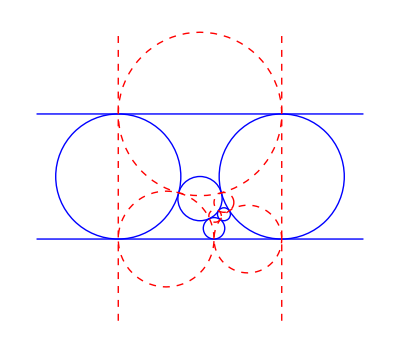
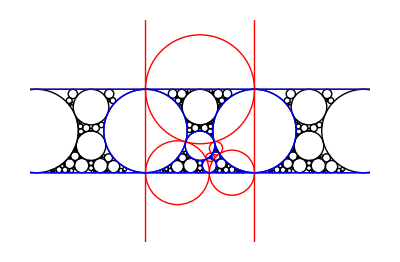
-Graphics-
-Graphics-
(16 | 1 | 2 √(2+√2) | -1+2 √2
0 | 1/(2 √2) | 0 | 1
16 (1+√2) | 1+3/(2 √2) | 2 √(10+7 √2) | 1
24 (2+√2) | 2+√2 | 1/382 (2035+√17610545) | 1+2 √2
8 (1+√2) | 1/(2 √2) | √(2 (2+√2)) | 1
8 √2 | 0 | 0 | 1
0 | 0 | 0 | -1
Root[562-261 #1-159 #1^2-5 #1^3+3 #1^4&,2] | Root[1-16 #1^2+32 #1^4&,3] | 1 | 2 √(2-√2)
Root[-351-771 #1-253 #1^2-7 #1^3+#1^4&,4] | 1/2 √(1+1/(√2)) | 1+2 √2 | 0
Root[2591+288 #1-3716 #1^2+52 #1^3&,3] | 1/2 √(26+17 √2) | 7+6 √2 | 2 √(2+√2)
Root[-6193+621 #1-292 #1^2+5 #1^3&,1] | 1/2 √(10+7 √2) | 5+4 √2 | 2 √(2+√2)
0 | (√(2+√2))/4 | 1 | 0
0 | 0 | -1 | 0
Root[7+62 #1-29 #1^2+72 #1^3-51 #1^4-56 #1^5+4 #1^6&,4] | 0 | 1 | 0)
{{(0 | (5-48 √(4-2 √2)-144 √(2-√2)-216 √(2+√2)+192 √(2 (2+√2))+√(1297+12 (352344-14 √129627778)^(1/3)+12 (352344+14 √129627778)^(1/3))+√((2 (1016641+7782 (352344-14 √129627778)^(1/3)-72 (352344-14 √129627778)^(2/3)+7782 (352344+14 √129627778)^(1/3)-72 (352344+14 √129627778)^(2/3)+28457 √(1297+12 (352344-14 √129627778)^(1/3)+12 (352344+14 √129627778)^(1/3))))/(1297+12 (352344-14 √129627778)^(1/3)+12 (352344+14 √129627778)^(1/3))))/(12 √(2 (2+√2))) | 0 | 0 | (5/12-4 √(4-2 √2)+4 √(2-√2)-2 √(2+√2)+1/12 √(1297+12 (352344-14 √129627778)^(1/3)+12 (352344+14 √129627778)^(1/3))+1/(6 √(2/(1297-6 (352344-14 √129627778)^(1/3)-6 (352344+14 √129627778)^(1/3)+28457/(√(1297+12 (352344-14 √129627778)^(1/3)+12 (352344+14 √129627778)^(1/3)))))))/(√(2 (2+√2))) | 1/16 (-16+64 √2+4 √(4-2 √2) (5/12+1/12 √(1297+12 (352344-14 √129627778)^(1/3)+12 (352344+14 √129627778)^(1/3))+1/(6 √(2/(1297-6 (352344-14 √129627778)^(1/3)-6 (352344+14 √129627778)^(1/3)+28457/(√(1297+12 (352344-14 √129627778)^(1/3)+12 (352344+14 √129627778)^(1/3)))))))-8 √(2-√2) (5/12+1/12 √(1297+12 (352344-14 √129627778)^(1/3)+12 (352344+14 √129627778)^(1/3))+1/(6 √(2/(1297-6 (352344-14 √129627778)^(1/3)-6 (352344+14 √129627778)^(1/3)+28457/(√(1297+12 (352344-14 √129627778)^(1/3)+12 (352344+14 √129627778)^(1/3)))))))-8 √(2 (2+√2)) (5/12+1/12 √(1297+12 (352344-14 √129627778)^(1/3)+12 (352344+14 √129627778)^(1/3))+1/(6 √(2/(1297-6 (352344-14 √129627778)^(1/3)-6 (352344+14 √129627778)^(1/3)+28457/(√(1297+12 (352344-14 √129627778)^(1/3)+12 (352344+14 √129627778)^(1/3)))))))+√2 (5/12+1/12 √(1297+12 (352344-14 √129627778)^(1/3)+12 (352344+14 √129627778)^(1/3))+1/(6 √(2/(1297-6 (352344-14 √129627778)^(1/3)-6 (352344+14 √129627778)^(1/3)+28457/(√(1297+12 (352344-14 √129627778)^(1/3)+12 (352344+14 √129627778)^(1/3)))))))^2) | -38+46 √2-4 √(6-4 √2)-6 √(3-2 √2)-24 (-1+√2)+1/2 √(1-1/(√2)) (5/12+1/12 √(1297+12 (352344-14 √129627778)^(1/3)+12 (352344+14 √129627778)^(1/3))+1/(6 √(2/(1297-6 (352344-14 √129627778)^(1/3)-6 (352344+14 √129627778)^(1/3)+28457/(√(1297+12 (352344-14 √129627778)^(1/3)+12 (352344+14 √129627778)^(1/3)))))))-5/2 √(2-√2) (5/12+1/12 √(1297+12 (352344-14 √129627778)^(1/3)+12 (352344+14 √129627778)^(1/3))+1/(6 √(2/(1297-6 (352344-14 √129627778)^(1/3)-6 (352344+14 √129627778)^(1/3)+28457/(√(1297+12 (352344-14 √129627778)^(1/3)+12 (352344+14 √129627778)^(1/3)))))))-(5/12+1/12 √(1297+12 (352344-14 √129627778)^(1/3)+12 (352344+14 √129627778)^(1/3))+1/(6 √(2/(1297-6 (352344-14 √129627778)^(1/3)-6 (352344+14 √129627778)^(1/3)+28457/(√(1297+12 (352344-14 √129627778)^(1/3)+12 (352344+14 √129627778)^(1/3)))))))/(√(2+√2))+((5/12+1/12 √(1297+12 (352344-14 √129627778)^(1/3)+12 (352344+14 √129627778)^(1/3))+1/(6 √(2/(1297-6 (352344-14 √129627778)^(1/3)-6 (352344+14 √129627778)^(1/3)+28457/(√(1297+12 (352344-14 √129627778)^(1/3)+12 (352344+14 √129627778)^(1/3)))))))^2)/(8 √2)
0 | (5+96 √(4-2 √2)-336 √(2+√2)+192 √(2 (2+√2))+√(1297+12 (352344-14 √129627778)^(1/3)+12 (352344+14 √129627778)^(1/3))+√((2 (1016641+7782 (352344-14 √129627778)^(1/3)-72 (352344-14 √129627778)^(2/3)+7782 (352344+14 √129627778)^(1/3)-72 (352344+14 √129627778)^(2/3)+28457 √(1297+12 (352344-14 √129627778)^(1/3)+12 (352344+14 √129627778)^(1/3))))/(1297+12 (352344-14 √129627778)^(1/3)+12 (352344+14 √129627778)^(1/3))))/(48 √(2+√2)) | 0 | 0 | (5/12-8 √(4-2 √2)+1/12 √(1297+12 (352344-14 √129627778)^(1/3)+12 (352344+14 √129627778)^(1/3))+1/(6 √(2/(1297-6 (352344-14 √129627778)^(1/3)-6 (352344+14 √129627778)^(1/3)+28457/(√(1297+12 (352344-14 √129627778)^(1/3)+12 (352344+14 √129627778)^(1/3)))))))/(4 √(2+√2)) | 1/32 (64-8 √(4-2 √2) (5/12+1/12 √(1297+12 (352344-14 √129627778)^(1/3)+12 (352344+14 √129627778)^(1/3))+1/(6 √(2/(1297-6 (352344-14 √129627778)^(1/3)-6 (352344+14 √129627778)^(1/3)+28457/(√(1297+12 (352344-14 √129627778)^(1/3)+12 (352344+14 √129627778)^(1/3)))))))-4 √(2+√2) (5/12+1/12 √(1297+12 (352344-14 √129627778)^(1/3)+12 (352344+14 √129627778)^(1/3))+1/(6 √(2/(1297-6 (352344-14 √129627778)^(1/3)-6 (352344+14 √129627778)^(1/3)+28457/(√(1297+12 (352344-14 √129627778)^(1/3)+12 (352344+14 √129627778)^(1/3)))))))+(5/12+1/12 √(1297+12 (352344-14 √129627778)^(1/3)+12 (352344+14 √129627778)^(1/3))+1/(6 √(2/(1297-6 (352344-14 √129627778)^(1/3)-6 (352344+14 √129627778)^(1/3)+28457/(√(1297+12 (352344-14 √129627778)^(1/3)+12 (352344+14 √129627778)^(1/3)))))))^2) | 16-8 √2+2 √(6-4 √2)+2 √(3-2 √2)+4 (-2+√2)-√(1-1/(√2)) (5/12+1/12 √(1297+12 (352344-14 √129627778)^(1/3)+12 (352344+14 √129627778)^(1/3))+1/(6 √(2/(1297-6 (352344-14 √129627778)^(1/3)-6 (352344+14 √129627778)^(1/3)+28457/(√(1297+12 (352344-14 √129627778)^(1/3)+12 (352344+14 √129627778)^(1/3)))))))-(5/12+1/12 √(1297+12 (352344-14 √129627778)^(1/3)+12 (352344+14 √129627778)^(1/3))+1/(6 √(2/(1297-6 (352344-14 √129627778)^(1/3)-6 (352344+14 √129627778)^(1/3)+28457/(√(1297+12 (352344-14 √129627778)^(1/3)+12 (352344+14 √129627778)^(1/3)))))))/(4 √(2+√2))-(5/12+1/12 √(1297+12 (352344-14 √129627778)^(1/3)+12 (352344+14 √129627778)^(1/3))+1/(6 √(2/(1297-6 (352344-14 √129627778)^(1/3)-6 (352344+14 √129627778)^(1/3)+28457/(√(1297+12 (352344-14 √129627778)^(1/3)+12 (352344+14 √129627778)^(1/3)))))))/(4 √(2 (2+√2)))+1/32 (5/12+1/12 √(1297+12 (352344-14 √129627778)^(1/3)+12 (352344+14 √129627778)^(1/3))+1/(6 √(2/(1297-6 (352344-14 √129627778)^(1/3)-6 (352344+14 √129627778)^(1/3)+28457/(√(1297+12 (352344-14 √129627778)^(1/3)+12 (352344+14 √129627778)^(1/3)))))))^2
0 | (15+10 √2-96 √(4-2 √2)-192 √(2-√2)+144 √(2+√2)+288 √(2 (2+√2))-144 √(20+14 √2)+3 √(1297+12 (352344-14 √129627778)^(1/3)+12 (352344+14 √129627778)^(1/3))+2 √(2594+24 (352344-14 √129627778)^(1/3)+24 (352344+14 √129627778)^(1/3))+4 √((1016641+7782 (352344-14 √129627778)^(1/3)-72 (352344-14 √129627778)^(2/3)+7782 (352344+14 √129627778)^(1/3)-72 (352344+14 √129627778)^(2/3)+28457 √(1297+12 (352344-14 √129627778)^(1/3)+12 (352344+14 √129627778)^(1/3)))/(1297+12 (352344-14 √129627778)^(1/3)+12 (352344+14 √129627778)^(1/3)))+3 √((2 (1016641+7782 (352344-14 √129627778)^(1/3)-72 (352344-14 √129627778)^(2/3)+7782 (352344+14 √129627778)^(1/3)-72 (352344+14 √129627778)^(2/3)+28457 √(1297+12 (352344-14 √129627778)^(1/3)+12 (352344+14 √129627778)^(1/3))))/(1297+12 (352344-14 √129627778)^(1/3)+12 (352344+14 √129627778)^(1/3))))/(48 √(2+√2)) | 0 | 0 | (16 √(4-2 √2)+16 √(2-√2)-8 √(10+7 √2)+4 (5/12+1/12 √(1297+12 (352344-14 √129627778)^(1/3)+12 (352344+14 √129627778)^(1/3))+1/(6 √(2/(1297-6 (352344-14 √129627778)^(1/3)-6 (352344+14 √129627778)^(1/3)+28457/(√(1297+12 (352344-14 √129627778)^(1/3)+12 (352344+14 √129627778)^(1/3)))))))+3 √2 (5/12+1/12 √(1297+12 (352344-14 √129627778)^(1/3)+12 (352344+14 √129627778)^(1/3))+1/(6 √(2/(1297-6 (352344-14 √129627778)^(1/3)-6 (352344+14 √129627778)^(1/3)+28457/(√(1297+12 (352344-14 √129627778)^(1/3)+12 (352344+14 √129627778)^(1/3))))))))/(4 √(2 (2+√2))) | 1/32 (-32 √2+32 √(17+12 √2)+8 √(4-2 √2) (5/12+1/12 √(1297+12 (352344-14 √129627778)^(1/3)+12 (352344+14 √129627778)^(1/3))+1/(6 √(2/(1297-6 (352344-14 √129627778)^(1/3)-6 (352344+14 √129627778)^(1/3)+28457/(√(1297+12 (352344-14 √129627778)^(1/3)+12 (352344+14 √129627778)^(1/3)))))))+16 √(2-√2) (5/12+1/12 √(1297+12 (352344-14 √129627778)^(1/3)+12 (352344+14 √129627778)^(1/3))+1/(6 √(2/(1297-6 (352344-14 √129627778)^(1/3)-6 (352344+14 √129627778)^(1/3)+28457/(√(1297+12 (352344-14 √129627778)^(1/3)+12 (352344+14 √129627778)^(1/3)))))))-12 √(2+√2) (5/12+1/12 √(1297+12 (352344-14 √129627778)^(1/3)+12 (352344+14 √129627778)^(1/3))+1/(6 √(2/(1297-6 (352344-14 √129627778)^(1/3)-6 (352344+14 √129627778)^(1/3)+28457/(√(1297+12 (352344-14 √129627778)^(1/3)+12 (352344+14 √129627778)^(1/3)))))))-8 √(2 (2+√2)) (5/12+1/12 √(1297+12 (352344-14 √129627778)^(1/3)+12 (352344+14 √129627778)^(1/3))+1/(6 √(2/(1297-6 (352344-14 √129627778)^(1/3)-6 (352344+14 √129627778)^(1/3)+28457/(√(1297+12 (352344-14 √129627778)^(1/3)+12 (352344+14 √129627778)^(1/3)))))))-8 √(20+14 √2) (5/12+1/12 √(1297+12 (352344-14 √129627778)^(1/3)+12 (352344+14 √129627778)^(1/3))+1/(6 √(2/(1297-6 (352344-14 √129627778)^(1/3)-6 (352344+14 √129627778)^(1/3)+28457/(√(1297+12 (352344-14 √129627778)^(1/3)+12 (352344+14 √129627778)^(1/3)))))))+3 (5/12+1/12 √(1297+12 (352344-14 √129627778)^(1/3)+12 (352344+14 √129627778)^(1/3))+1/(6 √(2/(1297-6 (352344-14 √129627778)^(1/3)-6 (352344+14 √129627778)^(1/3)+28457/(√(1297+12 (352344-14 √129627778)^(1/3)+12 (352344+14 √129627778)^(1/3)))))))^2+2 √2 (5/12+1/12 √(1297+12 (352344-14 √129627778)^(1/3)+12 (352344+14 √129627778)^(1/3))+1/(6 √(2/(1297-6 (352344-14 √129627778)^(1/3)-6 (352344+14 √129627778)^(1/3)+28457/(√(1297+12 (352344-14 √129627778)^(1/3)+12 (352344+14 √129627778)^(1/3)))))))^2) | 28-13 √2-4 √(6-4 √2)-6 √(3-2 √2)+12 (-2+√2)+√(3+2 √2)+5 √(6+4 √2)-√(1-1/(√2)) (5/12+1/12 √(1297+12 (352344-14 √129627778)^(1/3)+12 (352344+14 √129627778)^(1/3))+1/(6 √(2/(1297-6 (352344-14 √129627778)^(1/3)-6 (352344+14 √129627778)^(1/3)+28457/(√(1297+12 (352344-14 √129627778)^(1/3)+12 (352344+14 √129627778)^(1/3)))))))-1/2 √(5+7/(√2)) (5/12+1/12 √(1297+12 (352344-14 √129627778)^(1/3)+12 (352344+14 √129627778)^(1/3))+1/(6 √(2/(1297-6 (352344-14 √129627778)^(1/3)-6 (352344+14 √129627778)^(1/3)+28457/(√(1297+12 (352344-14 √129627778)^(1/3)+12 (352344+14 √129627778)^(1/3)))))))-1/2 √(2-√2) (5/12+1/12 √(1297+12 (352344-14 √129627778)^(1/3)+12 (352344+14 √129627778)^(1/3))+1/(6 √(2/(1297-6 (352344-14 √129627778)^(1/3)-6 (352344+14 √129627778)^(1/3)+28457/(√(1297+12 (352344-14 √129627778)^(1/3)+12 (352344+14 √129627778)^(1/3)))))))-(5 (5/12+1/12 √(1297+12 (352344-14 √129627778)^(1/3)+12 (352344+14 √129627778)^(1/3))+1/(6 √(2/(1297-6 (352344-14 √129627778)^(1/3)-6 (352344+14 √129627778)^(1/3)+28457/(√(1297+12 (352344-14 √129627778)^(1/3)+12 (352344+14 √129627778)^(1/3))))))))/(4 √(2+√2))-(7 (5/12+1/12 √(1297+12 (352344-14 √129627778)^(1/3)+12 (352344+14 √129627778)^(1/3))+1/(6 √(2/(1297-6 (352344-14 √129627778)^(1/3)-6 (352344+14 √129627778)^(1/3)+28457/(√(1297+12 (352344-14 √129627778)^(1/3)+12 (352344+14 √129627778)^(1/3))))))))/(4 √(2 (2+√2)))+3/32 (5/12+1/12 √(1297+12 (352344-14 √129627778)^(1/3)+12 (352344+14 √129627778)^(1/3))+1/(6 √(2/(1297-6 (352344-14 √129627778)^(1/3)-6 (352344+14 √129627778)^(1/3)+28457/(√(1297+12 (352344-14 √129627778)^(1/3)+12 (352344+14 √129627778)^(1/3)))))))^2+((5/12+1/12 √(1297+12 (352344-14 √129627778)^(1/3)+12 (352344+14 √129627778)^(1/3))+1/(6 √(2/(1297-6 (352344-14 √129627778)^(1/3)-6 (352344+14 √129627778)^(1/3)+28457/(√(1297+12 (352344-14 √129627778)^(1/3)+12 (352344+14 √129627778)^(1/3)))))))^2)/(8 √2)
0 | (955-17360 √2-9 √35221090-9168 √(4-2 √2)-9168 √(2-√2)+27504 √(2+√2)+9168 √(2 (2+√2))+191 √(1297+12 (352344-14 √129627778)^(1/3)+12 (352344+14 √129627778)^(1/3))+191 √(2594+24 (352344-14 √129627778)^(1/3)+24 (352344+14 √129627778)^(1/3))+382 √((1016641+7782 (352344-14 √129627778)^(1/3)-72 (352344-14 √129627778)^(2/3)+7782 (352344+14 √129627778)^(1/3)-72 (352344+14 √129627778)^(2/3)+28457 √(1297+12 (352344-14 √129627778)^(1/3)+12 (352344+14 √129627778)^(1/3)))/(1297+12 (352344-14 √129627778)^(1/3)+12 (352344+14 √129627778)^(1/3)))+191 √((2 (1016641+7782 (352344-14 √129627778)^(1/3)-72 (352344-14 √129627778)^(2/3)+7782 (352344+14 √129627778)^(1/3)-72 (352344+14 √129627778)^(2/3)+28457 √(1297+12 (352344-14 √129627778)^(1/3)+12 (352344+14 √129627778)^(1/3))))/(1297+12 (352344-14 √129627778)^(1/3)+12 (352344+14 √129627778)^(1/3))))/(2292 √(2+√2)) | 0 | 0 | (-2035-√17610545+1528 √(4-2 √2)+3056 √(2-√2)+764 (5/12+1/12 √(1297+12 (352344-14 √129627778)^(1/3)+12 (352344+14 √129627778)^(1/3))+1/(6 √(2/(1297-6 (352344-14 √129627778)^(1/3)-6 (352344+14 √129627778)^(1/3)+28457/(√(1297+12 (352344-14 √129627778)^(1/3)+12 (352344+14 √129627778)^(1/3)))))))+382 √2 (5/12+1/12 √(1297+12 (352344-14 √129627778)^(1/3)+12 (352344+14 √129627778)^(1/3))+1/(6 √(2/(1297-6 (352344-14 √129627778)^(1/3)-6 (352344+14 √129627778)^(1/3)+28457/(√(1297+12 (352344-14 √129627778)^(1/3)+12 (352344+14 √129627778)^(1/3))))))))/(382 √(2 (2+√2))) | (-3056+3056 √2+4070 √(2 (2+√2))+2 √(35221090 (2+√2))-2035 √2 (5/12+1/12 √(1297+12 (352344-14 √129627778)^(1/3)+12 (352344+14 √129627778)^(1/3))+1/(6 √(2/(1297-6 (352344-14 √129627778)^(1/3)-6 (352344+14 √129627778)^(1/3)+28457/(√(1297+12 (352344-14 √129627778)^(1/3)+12 (352344+14 √129627778)^(1/3)))))))-√35221090 (5/12+1/12 √(1297+12 (352344-14 √129627778)^(1/3)+12 (352344+14 √129627778)^(1/3))+1/(6 √(2/(1297-6 (352344-14 √129627778)^(1/3)-6 (352344+14 √129627778)^(1/3)+28457/(√(1297+12 (352344-14 √129627778)^(1/3)+12 (352344+14 √129627778)^(1/3)))))))+1528 √(4-2 √2) (5/12+1/12 √(1297+12 (352344-14 √129627778)^(1/3)+12 (352344+14 √129627778)^(1/3))+1/(6 √(2/(1297-6 (352344-14 √129627778)^(1/3)-6 (352344+14 √129627778)^(1/3)+28457/(√(1297+12 (352344-14 √129627778)^(1/3)+12 (352344+14 √129627778)^(1/3)))))))+1528 √(2-√2) (5/12+1/12 √(1297+12 (352344-14 √129627778)^(1/3)+12 (352344+14 √129627778)^(1/3))+1/(6 √(2/(1297-6 (352344-14 √129627778)^(1/3)-6 (352344+14 √129627778)^(1/3)+28457/(√(1297+12 (352344-14 √129627778)^(1/3)+12 (352344+14 √129627778)^(1/3)))))))-1528 √(2+√2) (5/12+1/12 √(1297+12 (352344-14 √129627778)^(1/3)+12 (352344+14 √129627778)^(1/3))+1/(6 √(2/(1297-6 (352344-14 √129627778)^(1/3)-6 (352344+14 √129627778)^(1/3)+28457/(√(1297+12 (352344-14 √129627778)^(1/3)+12 (352344+14 √129627778)^(1/3)))))))-1528 √(2 (2+√2)) (5/12+1/12 √(1297+12 (352344-14 √129627778)^(1/3)+12 (352344+14 √129627778)^(1/3))+1/(6 √(2/(1297-6 (352344-14 √129627778)^(1/3)-6 (352344+14 √129627778)^(1/3)+28457/(√(1297+12 (352344-14 √129627778)^(1/3)+12 (352344+14 √129627778)^(1/3)))))))+382 (5/12+1/12 √(1297+12 (352344-14 √129627778)^(1/3)+12 (352344+14 √129627778)^(1/3))+1/(6 √(2/(1297-6 (352344-14 √129627778)^(1/3)-6 (352344+14 √129627778)^(1/3)+28457/(√(1297+12 (352344-14 √129627778)^(1/3)+12 (352344+14 √129627778)^(1/3)))))))^2+382 √2 (5/12+1/12 √(1297+12 (352344-14 √129627778)^(1/3)+12 (352344+14 √129627778)^(1/3))+1/(6 √(2/(1297-6 (352344-14 √129627778)^(1/3)-6 (352344+14 √129627778)^(1/3)+28457/(√(1297+12 (352344-14 √129627778)^(1/3)+12 (352344+14 √129627778)^(1/3)))))))^2)/3056 | -10+29 √2-6 √(6-4 √2)-8 √(3-2 √2)+(2035 √(2-√2))/191+1/191 √(17610545 (2-√2))+16 (-2+√2)-40 (-1+√2)+1/382 √(17610545/(2 (2+√2)))+1/764 √(17610545/(2+√2))+2035/(764 √(2+√2))+2035/(382 √(2 (2+√2)))-(2035 (5/12+1/12 √(1297+12 (352344-14 √129627778)^(1/3)+12 (352344+14 √129627778)^(1/3))+1/(6 √(2/(1297-6 (352344-14 √129627778)^(1/3)-6 (352344+14 √129627778)^(1/3)+28457/(√(1297+12 (352344-14 √129627778)^(1/3)+12 (352344+14 √129627778)^(1/3))))))))/(1528 √2)-(√(17610545/2) (5/12+1/12 √(1297+12 (352344-14 √129627778)^(1/3)+12 (352344+14 √129627778)^(1/3))+1/(6 √(2/(1297-6 (352344-14 √129627778)^(1/3)-6 (352344+14 √129627778)^(1/3)+28457/(√(1297+12 (352344-14 √129627778)^(1/3)+12 (352344+14 √129627778)^(1/3))))))))/1528-√(1-1/(√2)) (5/12+1/12 √(1297+12 (352344-14 √129627778)^(1/3)+12 (352344+14 √129627778)^(1/3))+1/(6 √(2/(1297-6 (352344-14 √129627778)^(1/3)-6 (352344+14 √129627778)^(1/3)+28457/(√(1297+12 (352344-14 √129627778)^(1/3)+12 (352344+14 √129627778)^(1/3)))))))-3/2 √(2-√2) (5/12+1/12 √(1297+12 (352344-14 √129627778)^(1/3)+12 (352344+14 √129627778)^(1/3))+1/(6 √(2/(1297-6 (352344-14 √129627778)^(1/3)-6 (352344+14 √129627778)^(1/3)+28457/(√(1297+12 (352344-14 √129627778)^(1/3)+12 (352344+14 √129627778)^(1/3)))))))-(2 (5/12+1/12 √(1297+12 (352344-14 √129627778)^(1/3)+12 (352344+14 √129627778)^(1/3))+1/(6 √(2/(1297-6 (352344-14 √129627778)^(1/3)-6 (352344+14 √129627778)^(1/3)+28457/(√(1297+12 (352344-14 √129627778)^(1/3)+12 (352344+14 √129627778)^(1/3))))))))/(√(2+√2))-(3 (5/12+1/12 √(1297+12 (352344-14 √129627778)^(1/3)+12 (352344+14 √129627778)^(1/3))+1/(6 √(2/(1297-6 (352344-14 √129627778)^(1/3)-6 (352344+14 √129627778)^(1/3)+28457/(√(1297+12 (352344-14 √129627778)^(1/3)+12 (352344+14 √129627778)^(1/3))))))))/(√(2 (2+√2)))+1/8 (5/12+1/12 √(1297+12 (352344-14 √129627778)^(1/3)+12 (352344+14 √129627778)^(1/3))+1/(6 √(2/(1297-6 (352344-14 √129627778)^(1/3)-6 (352344+14 √129627778)^(1/3)+28457/(√(1297+12 (352344-14 √129627778)^(1/3)+12 (352344+14 √129627778)^(1/3)))))))^2+((5/12+1/12 √(1297+12 (352344-14 √129627778)^(1/3)+12 (352344+14 √129627778)^(1/3))+1/(6 √(2/(1297-6 (352344-14 √129627778)^(1/3)-6 (352344+14 √129627778)^(1/3)+28457/(√(1297+12 (352344-14 √129627778)^(1/3)+12 (352344+14 √129627778)^(1/3)))))))^2)/(4 √2)
0 | (5-192 √(4-2 √2)-288 √(2-√2)-96 √(2+√2)+192 √(2 (2+√2))+√(1297+12 (352344-14 √129627778)^(1/3)+12 (352344+14 √129627778)^(1/3))+√((2 (1016641+7782 (352344-14 √129627778)^(1/3)-72 (352344-14 √129627778)^(2/3)+7782 (352344+14 √129627778)^(1/3)-72 (352344+14 √129627778)^(2/3)+28457 √(1297+12 (352344-14 √129627778)^(1/3)+12 (352344+14 √129627778)^(1/3))))/(1297+12 (352344-14 √129627778)^(1/3)+12 (352344+14 √129627778)^(1/3))))/(48 √(2+√2)) | 0 | 0 | (5/12+8 √(2-√2)-4 √(2+√2)+1/12 √(1297+12 (352344-14 √129627778)^(1/3)+12 (352344+14 √129627778)^(1/3))+1/(6 √(2/(1297-6 (352344-14 √129627778)^(1/3)-6 (352344+14 √129627778)^(1/3)+28457/(√(1297+12 (352344-14 √129627778)^(1/3)+12 (352344+14 √129627778)^(1/3)))))))/(4 √(2+√2)) | 2+1/4 √(2-√2) (5/12+1/12 √(1297+12 (352344-14 √129627778)^(1/3)+12 (352344+14 √129627778)^(1/3))+1/(6 √(2/(1297-6 (352344-14 √129627778)^(1/3)-6 (352344+14 √129627778)^(1/3)+28457/(√(1297+12 (352344-14 √129627778)^(1/3)+12 (352344+14 √129627778)^(1/3)))))))-3/8 √(2+√2) (5/12+1/12 √(1297+12 (352344-14 √129627778)^(1/3)+12 (352344+14 √129627778)^(1/3))+1/(6 √(2/(1297-6 (352344-14 √129627778)^(1/3)-6 (352344+14 √129627778)^(1/3)+28457/(√(1297+12 (352344-14 √129627778)^(1/3)+12 (352344+14 √129627778)^(1/3)))))))+1/32 (5/12+1/12 √(1297+12 (352344-14 √129627778)^(1/3)+12 (352344+14 √129627778)^(1/3))+1/(6 √(2/(1297-6 (352344-14 √129627778)^(1/3)-6 (352344+14 √129627778)^(1/3)+28457/(√(1297+12 (352344-14 √129627778)^(1/3)+12 (352344+14 √129627778)^(1/3)))))))^2 | 30-11 √2-5 √(6-4 √2)-6 √(3-2 √2)+8 (-2+√2)-1/2 √(1-1/(√2)) (5/12+1/12 √(1297+12 (352344-14 √129627778)^(1/3)+12 (352344+14 √129627778)^(1/3))+1/(6 √(2/(1297-6 (352344-14 √129627778)^(1/3)-6 (352344+14 √129627778)^(1/3)+28457/(√(1297+12 (352344-14 √129627778)^(1/3)+12 (352344+14 √129627778)^(1/3)))))))+1/4 √(2-√2) (5/12+1/12 √(1297+12 (352344-14 √129627778)^(1/3)+12 (352344+14 √129627778)^(1/3))+1/(6 √(2/(1297-6 (352344-14 √129627778)^(1/3)-6 (352344+14 √129627778)^(1/3)+28457/(√(1297+12 (352344-14 √129627778)^(1/3)+12 (352344+14 √129627778)^(1/3)))))))-(3 (5/12+1/12 √(1297+12 (352344-14 √129627778)^(1/3)+12 (352344+14 √129627778)^(1/3))+1/(6 √(2/(1297-6 (352344-14 √129627778)^(1/3)-6 (352344+14 √129627778)^(1/3)+28457/(√(1297+12 (352344-14 √129627778)^(1/3)+12 (352344+14 √129627778)^(1/3))))))))/(4 √(2+√2))-(3 (5/12+1/12 √(1297+12 (352344-14 √129627778)^(1/3)+12 (352344+14 √129627778)^(1/3))+1/(6 √(2/(1297-6 (352344-14 √129627778)^(1/3)-6 (352344+14 √129627778)^(1/3)+28457/(√(1297+12 (352344-14 √129627778)^(1/3)+12 (352344+14 √129627778)^(1/3))))))))/(4 √(2 (2+√2)))+1/32 (5/12+1/12 √(1297+12 (352344-14 √129627778)^(1/3)+12 (352344+14 √129627778)^(1/3))+1/(6 √(2/(1297-6 (352344-14 √129627778)^(1/3)-6 (352344+14 √129627778)^(1/3)+28457/(√(1297+12 (352344-14 √129627778)^(1/3)+12 (352344+14 √129627778)^(1/3)))))))^2
0 | 0 | 0 | 0 | 0 | 1 | 0
0 | -2 (-4+2 √2+√(6-4 √2)) | 0 | 0 | 2 √(6-4 √2) | -2+1/4 √(4-2 √2) (5/12+1/12 √(1297+12 (352344-14 √129627778)^(1/3)+12 (352344+14 √129627778)^(1/3))+1/(6 √(2/(1297-6 (352344-14 √129627778)^(1/3)-6 (352344+14 √129627778)^(1/3)+28457/(√(1297+12 (352344-14 √129627778)^(1/3)+12 (352344+14 √129627778)^(1/3))))))) | -7+4 √2-2 √(6-4 √2)-2 √(3-2 √2)+1/2 √(1-1/(√2)) (5/12+1/12 √(1297+12 (352344-14 √129627778)^(1/3)+12 (352344+14 √129627778)^(1/3))+1/(6 √(2/(1297-6 (352344-14 √129627778)^(1/3)-6 (352344+14 √129627778)^(1/3)+28457/(√(1297+12 (352344-14 √129627778)^(1/3)+12 (352344+14 √129627778)^(1/3)))))))),nonintegral},{(0 | 20+19 √2-16 √(3+2 √2)-4 √(6+4 √2)+Root[-351-771 #1-253 #1^2-7 #1^3+#1^4&,4]/(√(2 (2+√2))) | 0 | 0 | -12-9 √2+((4+√2) Root[-351-771 #1-253 #1^2-7 #1^3+#1^4&,4])/(2 √(2+√2)) | 1/16 (336+256 √2-24 √(2+√2) Root[-351-771 #1-253 #1^2-7 #1^3+#1^4&,4]-8 √(2 (2+√2)) Root[-351-771 #1-253 #1^2-7 #1^3+#1^4&,4]+√2 Root[-351-771 #1-253 #1^2-7 #1^3+#1^4&,4]^2) | 30-(32 √(10+7 √2)+8 √(20+14 √2)+(4+3 √2) Root[-351-771 #1-253 #1^2-7 #1^3+#1^4&,4])/(2 √(2+√2))+(384+Root[-351-771 #1-253 #1^2-7 #1^3+#1^4&,4]^2)/(8 √2)
0 | 1+Root[-351-771 #1-253 #1^2-7 #1^3+#1^4&,4]/(4 √(2+√2)) | 0 | 0 | ((1+2 √2) Root[-351-771 #1-253 #1^2-7 #1^3+#1^4&,4])/(4 √(2+√2)) | 1/32 Root[-351-771 #1-253 #1^2-7 #1^3+#1^4&,4] (-4 √(2+√2)-8 √(2 (2+√2))+Root[-351-771 #1-253 #1^2-7 #1^3+#1^4&,4]) | 1/32 Root[-351-771 #1-253 #1^2-7 #1^3+#1^4&,4] (-4 √(2+√2)+Root[-351-771 #1-253 #1^2-7 #1^3+#1^4&,4])
0 | (28 √(2+√2)+24 √(2 (2+√2))+64 √(10+7 √2)+68 √(20+14 √2)-64 √(58+41 √2)-16 √(116+82 √2)+3 Root[-351-771 #1-253 #1^2-7 #1^3+#1^4&,4]+2 √2 Root[-351-771 #1-253 #1^2-7 #1^3+#1^4&,4])/(4 √(2+√2)) | 0 | 0 | (80 √(2+√2)+48 √(2 (2+√2))-64 √(10+7 √2)-68 √(20+14 √2)+11 Root[-351-771 #1-253 #1^2-7 #1^3+#1^4&,4]+8 √2 Root[-351-771 #1-253 #1^2-7 #1^3+#1^4&,4])/(4 √(2+√2)) | 1/32 (-960-672 √2+544 √(17+12 √2)+256 √(34+24 √2)-28 √(2+√2) Root[-351-771 #1-253 #1^2-7 #1^3+#1^4&,4]-16 √(2 (2+√2)) Root[-351-771 #1-253 #1^2-7 #1^3+#1^4&,4]-32 √(10+7 √2) Root[-351-771 #1-253 #1^2-7 #1^3+#1^4&,4]-8 √(20+14 √2) Root[-351-771 #1-253 #1^2-7 #1^3+#1^4&,4]+3 Root[-351-771 #1-253 #1^2-7 #1^3+#1^4&,4]^2+2 √2 Root[-351-771 #1-253 #1^2-7 #1^3+#1^4&,4]^2) | -4+33 √(3+2 √2)+25 √(6+4 √2)+3/32 Root[-351-771 #1-253 #1^2-7 #1^3+#1^4&,4]^2-(128 √(58+41 √2)+32 √(116+82 √2)+(-6-5 √2+4 √(17+12 √2)+8 √(34+24 √2)) Root[-351-771 #1-253 #1^2-7 #1^3+#1^4&,4])/(8 √(2+√2))+(-48+Root[-351-771 #1-253 #1^2-7 #1^3+#1^4&,4]^2)/(8 √2)
0 | (-16280-6105 √2-8 √17610545-3 √35221090+12224 √(2+√2)+7640 √(2 (2+√2))+764 Root[-351-771 #1-253 #1^2-7 #1^3+#1^4&,4]+764 √2 Root[-351-771 #1-253 #1^2-7 #1^3+#1^4&,4])/(764 √(2+√2)) | 0 | 0 | (-34595-16280 √2-17 √17610545-8 √35221090+22920 √(2+√2)+13752 √(2 (2+√2))+2292 Root[-351-771 #1-253 #1^2-7 #1^3+#1^4&,4]+1910 √2 Root[-351-771 #1-253 #1^2-7 #1^3+#1^4&,4])/(382 √(2 (2+√2))) | (-192528-137520 √2+32 √(17610545 (2+√2))+34 √(35221090 (2+√2))+√(2+√2) (65120-3056 Root[-351-771 #1-253 #1^2-7 #1^3+#1^4&,4])+√(2 (2+√2)) (69190-2292 Root[-351-771 #1-253 #1^2-7 #1^3+#1^4&,4])-8140 Root[-351-771 #1-253 #1^2-7 #1^3+#1^4&,4]-2035 √2 Root[-351-771 #1-253 #1^2-7 #1^3+#1^4&,4]-4 √17610545 Root[-351-771 #1-253 #1^2-7 #1^3+#1^4&,4]-√35221090 Root[-351-771 #1-253 #1^2-7 #1^3+#1^4&,4]+382 Root[-351-771 #1-253 #1^2-7 #1^3+#1^4&,4]^2+382 √2 Root[-351-771 #1-253 #1^2-7 #1^3+#1^4&,4]^2)/3056 | (73260+40700 √2+36 √17610545+20 √35221090+7640 Root[-351-771 #1-253 #1^2-7 #1^3+#1^4&,4]+4584 √2 Root[-351-771 #1-253 #1^2-7 #1^3+#1^4&,4]-4 √(17610545 (2+√2)) Root[-351-771 #1-253 #1^2-7 #1^3+#1^4&,4]-√(35221090 (2+√2)) Root[-351-771 #1-253 #1^2-7 #1^3+#1^4&,4]+√(2+√2) (-36672-8140 Root[-351-771 #1-253 #1^2-7 #1^3+#1^4&,4]+382 Root[-351-771 #1-253 #1^2-7 #1^3+#1^4&,4]^2)+√(2 (2+√2)) (-21392-2035 Root[-351-771 #1-253 #1^2-7 #1^3+#1^4&,4]+382 Root[-351-771 #1-253 #1^2-7 #1^3+#1^4&,4]^2))/(3056 √(2+√2))
0 | (80 √(2+√2)+40 √(2 (2+√2))-16 √(10+7 √2)-32 √(20+14 √2)+Root[-351-771 #1-253 #1^2-7 #1^3+#1^4&,4])/(4 √(2+√2)) | 0 | 0 | -7-2 √2+((1+2 √2) Root[-351-771 #1-253 #1^2-7 #1^3+#1^4&,4])/(4 √(2+√2)) | 1/32 (320+192 √2-4 √(2+√2) Root[-351-771 #1-253 #1^2-7 #1^3+#1^4&,4]-16 √(2 (2+√2)) Root[-351-771 #1-253 #1^2-7 #1^3+#1^4&,4]+Root[-351-771 #1-253 #1^2-7 #1^3+#1^4&,4]^2) | 22+14 √2-4 √(3+2 √2)-8 √(6+4 √2)-5/8 √(2-√2) Root[-351-771 #1-253 #1^2-7 #1^3+#1^4&,4]-(3 Root[-351-771 #1-253 #1^2-7 #1^3+#1^4&,4])/(4 √(2+√2))+1/32 Root[-351-771 #1-253 #1^2-7 #1^3+#1^4&,4]^2
0 | 2 √2 | 0 | 0 | 2 (4+√2) | -9-6 √2+1/2 √(1+1/(√2)) Root[-351-771 #1-253 #1^2-7 #1^3+#1^4&,4] | 1/4 (-8 (1+√2)+√(2 (2+√2)) Root[-351-771 #1-253 #1^2-7 #1^3+#1^4&,4])
0 | 0 | 0 | 0 | 0 | 0 | 1),nonintegral},{(0 | (1280 √(2+√2)+970 √(2 (2+√2))-96 √(26+17 √2)-56 √(52+34 √2)-96 √(146+103 √2)-128 √(292+206 √2)-12 Root[2591+288 #1-3716 #1^2+52 #1^3&,3]-7 √2 Root[2591+288 #1-3716 #1^2+52 #1^3&,3]+4 √(43+30 √2) Root[2591+288 #1-3716 #1^2+52 #1^3&,3])/(2 √(2+√2)) | 0 | 0 | -368-275 √2+((12+7 √2) (8 √(26+17 √2)+Root[2591+288 #1-3716 #1^2+52 #1^3&,3]))/(2 √(2+√2)) | 643+460 √2-28 √(43+30 √2)-24 √(86+60 √2)-13/2 √(1+1/(√2)) Root[2591+288 #1-3716 #1^2+52 #1^3&,3]+√(13+17/(√2)) Root[2591+288 #1-3716 #1^2+52 #1^3&,3]-7 √(2+√2) Root[2591+288 #1-3716 #1^2+52 #1^3&,3]+(Root[2591+288 #1-3716 #1^2+52 #1^3&,3]^2)/(8 √2) | 1140-(152 √(26+17 √2)+104 √(52+34 √2)+96 √(146+103 √2)+160 √(292+206 √2)+49 Root[2591+288 #1-3716 #1^2+52 #1^3&,3]+31 √2 Root[2591+288 #1-3716 #1^2+52 #1^3&,3]-6 √(43+30 √2) Root[2591+288 #1-3716 #1^2+52 #1^3&,3])/(2 √(2+√2))+(13504+Root[2591+288 #1-3716 #1^2+52 #1^3&,3]^2)/(8 √2)
0 | (100 √(2+√2)+56 √(2 (2+√2))-32 √(146+103 √2)-7 Root[2591+288 #1-3716 #1^2+52 #1^3&,3]-6 √2 Root[2591+288 #1-3716 #1^2+52 #1^3&,3]+2 √(86+60 √2) Root[2591+288 #1-3716 #1^2+52 #1^3&,3])/(4 √(2+√2)) | 0 | 0 | -24-14 √2+((7+6 √2) Root[2591+288 #1-3716 #1^2+52 #1^3&,3])/(4 √(2+√2)) | 38+26 √2-7/8 √(2+√2) Root[2591+288 #1-3716 #1^2+52 #1^3&,3]-√(2 (2+√2)) Root[2591+288 #1-3716 #1^2+52 #1^3&,3]+1/32 Root[2591+288 #1-3716 #1^2+52 #1^3&,3]^2 | 54+34 √2-8 √(43+30 √2)+((-38-31 √2+4 √(86+60 √2)) Root[2591+288 #1-3716 #1^2+52 #1^3&,3])/(8 √(2+√2))+1/32 Root[2591+288 #1-3716 #1^2+52 #1^3&,3]^2
0 | (2860 √(2+√2)+1984 √(2 (2+√2))+1344 √(10+7 √2)+964 √(20+14 √2)-416 √(26+17 √2)-304 √(52+34 √2)-32 √(146+103 √2)-224 √(850+601 √2)-192 √(2 (850+601 √2))-45 Root[2591+288 #1-3716 #1^2+52 #1^3&,3]-32 √2 Root[2591+288 #1-3716 #1^2+52 #1^3&,3]+8 √(43+30 √2) Root[2591+288 #1-3716 #1^2+52 #1^3&,3]+6 √(86+60 √2) Root[2591+288 #1-3716 #1^2+52 #1^3&,3])/(4 √(2+√2)) | 0 | 0 | (-112 √(2+√2)-96 √(2 (2+√2))-1928 √(10+7 √2)-1344 √(20+14 √2)+608 √(26+17 √2)+416 √(52+34 √2)+64 Root[2591+288 #1-3716 #1^2+52 #1^3&,3]+45 √2 Root[2591+288 #1-3716 #1^2+52 #1^3&,3])/(4 √(2 (2+√2))) | 40+27 √2+241 √(17+12 √2)+168 √(34+24 √2)-76 √(43+30 √2)-52 √(86+60 √2)-17/2 √(1+1/(√2)) Root[2591+288 #1-3716 #1^2+52 #1^3&,3]-7/2 √(5+7/(√2)) Root[2591+288 #1-3716 #1^2+52 #1^3&,3]+√(13+17/(√2)) Root[2591+288 #1-3716 #1^2+52 #1^3&,3]-45/8 √(2+√2) Root[2591+288 #1-3716 #1^2+52 #1^3&,3]-3 √(10+7 √2) Root[2591+288 #1-3716 #1^2+52 #1^3&,3]+√(26+17 √2) Root[2591+288 #1-3716 #1^2+52 #1^3&,3]+3/32 Root[2591+288 #1-3716 #1^2+52 #1^3&,3]^2+(Root[2591+288 #1-3716 #1^2+52 #1^3&,3]^2)/(8 √2) | 746+(3 Root[875758+3744 #1-1858 #1^2+#1^3&,3]^2)/21632+(9232 √(10+7 √2)+6544 √(20+14 √2)-2880 √(26+17 √2)-2048 √(52+34 √2)+1536 √(58+41 √2)+896 √(116+82 √2)-640 √(146+103 √2)-256 √(292+206 √2)-896 √(850+601 √2)-768 √(2 (850+601 √2))-428 Root[2591+288 #1-3716 #1^2+52 #1^3&,3]-306 √2 Root[2591+288 #1-3716 #1^2+52 #1^3&,3]-56 √(17+12 √2) Root[2591+288 #1-3716 #1^2+52 #1^3&,3]-48 √(34+24 √2) Root[2591+288 #1-3716 #1^2+52 #1^3&,3]+48 √(43+30 √2) Root[2591+288 #1-3716 #1^2+52 #1^3&,3]+40 √(86+60 √2) Root[2591+288 #1-3716 #1^2+52 #1^3&,3]+√(2 (2+√2)) (8272+Root[2591+288 #1-3716 #1^2+52 #1^3&,3]^2))/(16 √(2+√2))
0 | (683760+490435 √2+336 √17610545+241 √35221090+1164336 √(2+√2)+838872 √(2 (2+√2))-174192 √(26+17 √2)-113960 √(43+30 √2)-56 √(17610545 (43+30 √2))-48 √(35221090 (43+30 √2))-119184 √(52+34 √2)-97680 √(86+60 √2)-6112 √(146+103 √2)-12224 √(292+206 √2)-14516 Root[2591+288 #1-3716 #1^2+52 #1^3&,3]-9932 √2 Root[2591+288 #1-3716 #1^2+52 #1^3&,3]+3056 √(43+30 √2) Root[2591+288 #1-3716 #1^2+52 #1^3&,3]+1528 √(86+60 √2) Root[2591+288 #1-3716 #1^2+52 #1^3&,3])/(764 √(2+√2)) | 0 | 0 | (-490435-341880 √2-241 √17610545-168 √35221090-47368 √(2+√2)-30560 √(2 (2+√2))+119184 √(26+17 √2)+87096 √(52+34 √2)+382 Root[875758+3744 #1-1858 #1^2+#1^3&,3]+7258 √2 Root[2591+288 #1-3716 #1^2+52 #1^3&,3])/(382 √(2 (2+√2))) | (443120+320880 √2+672 √(17610545 (2+√2))+482 √(35221090 (2+√2))-476736 √(43+30 √2)-348384 √(86+60 √2)+√(2 (2+√2)) (980870-20628 Root[2591+288 #1-3716 #1^2+52 #1^3&,3])-24420 Root[2591+288 #1-3716 #1^2+52 #1^3&,3]-14245 √2 Root[2591+288 #1-3716 #1^2+52 #1^3&,3]-12 √17610545 Root[2591+288 #1-3716 #1^2+52 #1^3&,3]-7 √35221090 Root[2591+288 #1-3716 #1^2+52 #1^3&,3]+4584 √(26+17 √2) Root[2591+288 #1-3716 #1^2+52 #1^3&,3]+4584 √(52+34 √2) Root[2591+288 #1-3716 #1^2+52 #1^3&,3]+382 Root[2591+288 #1-3716 #1^2+52 #1^3&,3]^2+382 √2 Root[2591+288 #1-3716 #1^2+52 #1^3&,3]^2-168 √(2+√2) (-8140+191 Root[2591+288 #1-3716 #1^2+52 #1^3&,3]))/3056 | (6389900+4566540 √2+3140 √17610545+2244 √35221090-1173504 √(26+17 √2)-455840 √(43+30 √2)-224 √(17610545 (43+30 √2))-192 √(35221090 (43+30 √2))-825120 √(52+34 √2)-390720 √(86+60 √2)-171136 √(146+103 √2)-195584 √(292+206 √2)-142104 Root[2591+288 #1-3716 #1^2+52 #1^3&,3]-97792 √2 Root[2591+288 #1-3716 #1^2+52 #1^3&,3]-12 √(17610545 (2+√2)) Root[2591+288 #1-3716 #1^2+52 #1^3&,3]-7 √(35221090 (2+√2)) Root[2591+288 #1-3716 #1^2+52 #1^3&,3]+21392 √(43+30 √2) Root[2591+288 #1-3716 #1^2+52 #1^3&,3]+10696 √(86+60 √2) Root[2591+288 #1-3716 #1^2+52 #1^3&,3]+√(2+√2) (4999616-24420 Root[2591+288 #1-3716 #1^2+52 #1^3&,3]+382 Root[2591+288 #1-3716 #1^2+52 #1^3&,3]^2)+√(2 (2+√2)) (3603024-14245 Root[2591+288 #1-3716 #1^2+52 #1^3&,3]+382 Root[2591+288 #1-3716 #1^2+52 #1^3&,3]^2))/(3056 √(2+√2))
0 | (2440 √(2+√2)+1688 √(2 (2+√2))-208 √(26+17 √2)-152 √(52+34 √2)-224 √(146+103 √2)-112 √(292+206 √2)-7 Root[2591+288 #1-3716 #1^2+52 #1^3&,3]-6 √2 Root[2591+288 #1-3716 #1^2+52 #1^3&,3]+2 √(86+60 √2) Root[2591+288 #1-3716 #1^2+52 #1^3&,3])/(4 √(2+√2)) | 0 | 0 | (-1060 √(2+√2)-728 √(2 (2+√2))+208 √(26+17 √2)+152 √(52+34 √2)+7 Root[2591+288 #1-3716 #1^2+52 #1^3&,3]+6 √2 Root[2591+288 #1-3716 #1^2+52 #1^3&,3])/(4 √(2+√2)) | 1/32 (14336+10080 √2-1216 √(43+30 √2)-832 √(86+60 √2)-84 √(2+√2) Root[2591+288 #1-3716 #1^2+52 #1^3&,3]-80 √(2 (2+√2)) Root[2591+288 #1-3716 #1^2+52 #1^3&,3]+16 √(26+17 √2) Root[2591+288 #1-3716 #1^2+52 #1^3&,3]+8 √(52+34 √2) Root[2591+288 #1-3716 #1^2+52 #1^3&,3]+Root[2591+288 #1-3716 #1^2+52 #1^3&,3]^2) | 960-90 √(9+4 √2)+1/32 Root[2591+288 #1-3716 #1^2+52 #1^3&,3]^2+(5336 √(2 (2+√2))-512 √(52+34 √2)-576 √(146+103 √2)-288 √(292+206 √2)-90 Root[2591+288 #1-3716 #1^2+52 #1^3&,3]-69 √2 Root[2591+288 #1-3716 #1^2+52 #1^3&,3]+4 √(43+30 √2) Root[2591+288 #1-3716 #1^2+52 #1^3&,3]+8 √(86+60 √2) Root[2591+288 #1-3716 #1^2+52 #1^3&,3])/(8 √(2+√2))
0 | 232+150 √2-28 √(9+4 √2)-24 √(18+8 √2)-8 √(43+30 √2) | 0 | 0 | -24-14 √2+28 √(9+4 √2)+24 √(18+8 √2) | 39+26 √2-52 √(9+4 √2)-38 √(18+8 √2)-1/2 √(1+1/(√2)) Root[2591+288 #1-3716 #1^2+52 #1^3&,3]+1/2 √(26+17 √2) Root[2591+288 #1-3716 #1^2+52 #1^3&,3] | 262+170 √2-52 √(9+4 √2)-38 √(18+8 √2)-24 √(43+30 √2)-1/2 √(1+1/(√2)) Root[2591+288 #1-3716 #1^2+52 #1^3&,3]+1/2 √(26+17 √2) Root[2591+288 #1-3716 #1^2+52 #1^3&,3]
0 | -24-14 √2+8 √(43+30 √2) | 0 | 0 | 24+14 √2 | -38-26 √2+1/2 √(1+1/(√2)) Root[2591+288 #1-3716 #1^2+52 #1^3&,3] | -53-34 √2+8 √(43+30 √2)+1/2 √(1+1/(√2)) Root[2591+288 #1-3716 #1^2+52 #1^3&,3]),nonintegral},{(0 | 296+217 √2-32 √(3+2 √2)-20 √(6+4 √2)-32 √(17+12 √2)-48 √(34+24 √2)-(4 (292+(1/2 (45814511-15 √1540435371501))^(1/3)+(1/2 (45814511+15 √1540435371501))^(1/3)))/(15 √(2+√2))-(292+(1/2 (45814511-15 √1540435371501))^(1/3)+(1/2 (45814511+15 √1540435371501))^(1/3))/(3 √(2 (2+√2)))+1/15 √(20+14 √2) (292+(1/2 (45814511-15 √1540435371501))^(1/3)+(1/2 (45814511+15 √1540435371501))^(1/3)) | 0 | 0 | (-368 √(2+√2)-270 √(2 (2+√2))+64 √(10+7 √2)+40 √(20+14 √2)+8/15 (292+(1/2 (45814511-15 √1540435371501))^(1/3)+(1/2 (45814511+15 √1540435371501))^(1/3))+1/3 √2 (292+(1/2 (45814511-15 √1540435371501))^(1/3)+(1/2 (45814511+15 √1540435371501))^(1/3)))/(2 √(2+√2)) | 319+228 √2-20 √(17+12 √2)-16 √(34+24 √2)-3/10 √(1+1/(√2)) (292+(1/2 (45814511-15 √1540435371501))^(1/3)+(1/2 (45814511+15 √1540435371501))^(1/3))+1/15 √(5+7/(√2)) (292+(1/2 (45814511-15 √1540435371501))^(1/3)+(1/2 (45814511+15 √1540435371501))^(1/3))-1/3 √(2+√2) (292+(1/2 (45814511-15 √1540435371501))^(1/3)+(1/2 (45814511+15 √1540435371501))^(1/3))+((292+(1/2 (45814511-15 √1540435371501))^(1/3)+(1/2 (45814511+15 √1540435371501))^(1/3))^2)/(1800 √2) | 592+436 √2-52 √(3+2 √2)-36 √(6+4 √2)-32 √(17+12 √2)-64 √(34+24 √2)+1/5 √(5+7/(√2)) (292+(1/2 (45814511-15 √1540435371501))^(1/3)+(1/2 (45814511+15 √1540435371501))^(1/3))-(37 (292+(1/2 (45814511-15 √1540435371501))^(1/3)+(1/2 (45814511+15 √1540435371501))^(1/3)))/(30 √(2+√2))-(23 (292+(1/2 (45814511-15 √1540435371501))^(1/3)+(1/2 (45814511+15 √1540435371501))^(1/3)))/(15 √(2 (2+√2)))+((292+(1/2 (45814511-15 √1540435371501))^(1/3)+(1/2 (45814511+15 √1540435371501))^(1/3))^2)/(1800 √2)
0 | 17+10 √2-8 √(17+12 √2)-1/15 √(2-√2) (292+(1/2 (45814511-15 √1540435371501))^(1/3)+(1/2 (45814511+15 √1540435371501))^(1/3))-(292+(1/2 (45814511-15 √1540435371501))^(1/3)+(1/2 (45814511+15 √1540435371501))^(1/3))/(12 √(2+√2))+1/30 √(10+7 √2) (292+(1/2 (45814511-15 √1540435371501))^(1/3)+(1/2 (45814511+15 √1540435371501))^(1/3)) | 0 | 0 | -16-10 √2+1/15 √(2-√2) (292+(1/2 (45814511-15 √1540435371501))^(1/3)+(1/2 (45814511+15 √1540435371501))^(1/3))+(584+2^(2/3) (45814511-15 √1540435371501)^(1/3)+2^(2/3) (45814511+15 √1540435371501)^(1/3))/(24 √(2+√2)) | 26+18 √2-1/10 √(1+1/(√2)) (292+(1/2 (45814511-15 √1540435371501))^(1/3)+(1/2 (45814511+15 √1540435371501))^(1/3))-1/24 √(2+√2) (292+(1/2 (45814511-15 √1540435371501))^(1/3)+(1/2 (45814511+15 √1540435371501))^(1/3))+((292+(1/2 (45814511-15 √1540435371501))^(1/3)+(1/2 (45814511+15 √1540435371501))^(1/3))^2)/7200 | 42+26 √2-8 √(17+12 √2)-(292+(1/2 (45814511-15 √1540435371501))^(1/3)+(1/2 (45814511+15 √1540435371501))^(1/3))/(4 √(2+√2))-(5 (292+(1/2 (45814511-15 √1540435371501))^(1/3)+(1/2 (45814511+15 √1540435371501))^(1/3)))/(12 √(2 (2+√2)))+1/30 √(10+7 √2) (292+(1/2 (45814511-15 √1540435371501))^(1/3)+(1/2 (45814511+15 √1540435371501))^(1/3))+((292+(1/2 (45814511-15 √1540435371501))^(1/3)+(1/2 (45814511+15 √1540435371501))^(1/3))^2)/7200
0 | -309-220 √2+88 √(3+2 √2)+61 √(6+4 √2)-8 √(17+12 √2)-(31 (292+(1/2 (45814511-15 √1540435371501))^(1/3)+(1/2 (45814511+15 √1540435371501))^(1/3)))/(60 √(2+√2))-(11 (292+(1/2 (45814511-15 √1540435371501))^(1/3)+(1/2 (45814511+15 √1540435371501))^(1/3)))/(15 √(2 (2+√2)))+1/10 √(10+7 √2) (292+(1/2 (45814511-15 √1540435371501))^(1/3)+(1/2 (45814511+15 √1540435371501))^(1/3))+1/15 √(20+14 √2) (292+(1/2 (45814511-15 √1540435371501))^(1/3)+(1/2 (45814511+15 √1540435371501))^(1/3)) | 0 | 0 | -(64 √(2+√2)+40 √(2 (2+√2))+352 √(10+7 √2)+244 √(20+14 √2)-31/15 (292+(1/2 (45814511-15 √1540435371501))^(1/3)+(1/2 (45814511+15 √1540435371501))^(1/3))-22/15 √2 (292+(1/2 (45814511-15 √1540435371501))^(1/3)+(1/2 (45814511+15 √1540435371501))^(1/3)))/(4 √(2+√2)) | 28+19 √2+61 √(17+12 √2)+44 √(34+24 √2)-1/10 √(5+7/(√2)) (292+(1/2 (45814511-15 √1540435371501))^(1/3)+(1/2 (45814511+15 √1540435371501))^(1/3))-31/120 √(2+√2) (292+(1/2 (45814511-15 √1540435371501))^(1/3)+(1/2 (45814511+15 √1540435371501))^(1/3))-1/5 √(2 (2+√2)) (292+(1/2 (45814511-15 √1540435371501))^(1/3)+(1/2 (45814511+15 √1540435371501))^(1/3))-1/15 √(10+7 √2) (292+(1/2 (45814511-15 √1540435371501))^(1/3)+(1/2 (45814511+15 √1540435371501))^(1/3))+((292+(1/2 (45814511-15 √1540435371501))^(1/3)+(1/2 (45814511+15 √1540435371501))^(1/3))^2)/2400+((292+(1/2 (45814511-15 √1540435371501))^(1/3)+(1/2 (45814511+15 √1540435371501))^(1/3))^2)/(1800 √2) | -282-203 √2+149 √(3+2 √2)+105 √(6+4 √2)+24 √(17+12 √2)+24 √(34+24 √2)+1/30 √(5+7/(√2)) (292+(1/2 (45814511-15 √1540435371501))^(1/3)+(1/2 (45814511+15 √1540435371501))^(1/3))-(83 (292+(1/2 (45814511-15 √1540435371501))^(1/3)+(1/2 (45814511+15 √1540435371501))^(1/3)))/(60 √(2+√2))-(119 (292+(1/2 (45814511-15 √1540435371501))^(1/3)+(1/2 (45814511+15 √1540435371501))^(1/3)))/(60 √(2 (2+√2)))+1/30 √(10+7 √2) (292+(1/2 (45814511-15 √1540435371501))^(1/3)+(1/2 (45814511+15 √1540435371501))^(1/3))+((292+(1/2 (45814511-15 √1540435371501))^(1/3)+(1/2 (45814511+15 √1540435371501))^(1/3))^2)/2400+((292+(1/2 (45814511-15 √1540435371501))^(1/3)+(1/2 (45814511+15 √1540435371501))^(1/3))^2)/(1800 √2)
0 | (1983856+1441533 √2+2400 √17610545+1695 √35221090+7288560 √(2+√2)+5202840 √(2 (2+√2))-1787760 √(10+7 √2)-328648 √(17+12 √2)-600 √(17610545 (17+12 √2))-480 √(35221090 (17+12 √2))-1237680 √(20+14 √2)-530624 √(34+24 √2)-91680 √(58+41 √2)-183360 √(116+82 √2)-6876 2^(1/6) (45814511-15 √1540435371501)^(1/3)-4966 2^(2/3) (45814511-15 √1540435371501)^(1/3)+1528 2^(1/6) √(17+12 √2) (45814511-15 √1540435371501)^(1/3)+1528 2^(2/3) √(17+12 √2) (45814511-15 √1540435371501)^(1/3)-6876 2^(1/6) (45814511+15 √1540435371501)^(1/3)-4966 2^(2/3) (45814511+15 √1540435371501)^(1/3)+1528 2^(1/6) √(17+12 √2) (45814511+15 √1540435371501)^(1/3)+1528 2^(2/3) √(17+12 √2) (45814511+15 √1540435371501)^(1/3))/(11460 √(2+√2)) | 0 | 0 | -(229955+162800 √2+113 √17610545+80 √35221090+32088 √(2+√2)+21392 √(2 (2+√2))-82512 √(10+7 √2)-59592 √(20+14 √2)-2292/5 (292+(1/2 (45814511-15 √1540435371501))^(1/3)+(1/2 (45814511+15 √1540435371501))^(1/3))-4966/15 √2 (292+(1/2 (45814511-15 √1540435371501))^(1/3)+(1/2 (45814511+15 √1540435371501))^(1/3)))/(382 √(2 (2+√2))) | (308656+223088 √2+651200 √(2+√2)+459910 √(2 (2+√2))+320 √(17610545 (2+√2))+226 √(35221090 (2+√2))-330048 √(17+12 √2)-238368 √(34+24 √2)-3256/3 (292+(1/2 (45814511-15 √1540435371501))^(1/3)+(1/2 (45814511+15 √1540435371501))^(1/3))-2035/3 √2 (292+(1/2 (45814511-15 √1540435371501))^(1/3)+(1/2 (45814511+15 √1540435371501))^(1/3))-8/3 √(3522109/5) (292+(1/2 (45814511-15 √1540435371501))^(1/3)+(1/2 (45814511+15 √1540435371501))^(1/3))-1/3 √35221090 (292+(1/2 (45814511-15 √1540435371501))^(1/3)+(1/2 (45814511+15 √1540435371501))^(1/3))-1528 √(2+√2) (292+(1/2 (45814511-15 √1540435371501))^(1/3)+(1/2 (45814511+15 √1540435371501))^(1/3))-14516/15 √(2 (2+√2)) (292+(1/2 (45814511-15 √1540435371501))^(1/3)+(1/2 (45814511+15 √1540435371501))^(1/3))+1528/5 √(10+7 √2) (292+(1/2 (45814511-15 √1540435371501))^(1/3)+(1/2 (45814511+15 √1540435371501))^(1/3))+1528/5 √(20+14 √2) (292+(1/2 (45814511-15 √1540435371501))^(1/3)+(1/2 (45814511+15 √1540435371501))^(1/3))+382/225 (292+(1/2 (45814511-15 √1540435371501))^(1/3)+(1/2 (45814511+15 √1540435371501))^(1/3))^2+382/225 √2 (292+(1/2 (45814511-15 √1540435371501))^(1/3)+(1/2 (45814511+15 √1540435371501))^(1/3))^2)/3056 | (519862284+405644184 √2+(70463 2^(1/6)-10556 2^(2/3)) (45814511-15 √1540435371501)^(1/3)+191 (2^(1/3)+2^(5/6)) (45814511-15 √1540435371501)^(2/3)+(70463 2^(1/6)-10556 2^(2/3)) (45814511+15 √1540435371501)^(1/3)+191 (2^(1/3)+2^(5/6)) (45814511+15 √1540435371501)^(2/3)-15 √17610545 (2336+2^(1/6) (5+4 √2) (45814511-15 √1540435371501)^(1/3)+2^(1/6) (5+4 √2) (45814511+15 √1540435371501)^(1/3))-(60 (-4586213-3488725 √2-6255 √17610545-4455 √35221090+365 √(35221090 (2+√2))+3025440 √(10+7 √2)-340616 √(17+12 √2)+600 √(17610545 (17+12 √2))+480 √(35221090 (17+12 √2))+2131560 √(20+14 √2)+195992 √(34+24 √2)+641760 √(58+41 √2)+733440 √(116+82 √2)+19100 2^(1/6) (45814511-15 √1540435371501)^(1/3)+13943 2^(2/3) (45814511-15 √1540435371501)^(1/3)-2674 2^(1/6) √(17+12 √2) (45814511-15 √1540435371501)^(1/3)-2674 2^(2/3) √(17+12 √2) (45814511-15 √1540435371501)^(1/3)+19100 2^(1/6) (45814511+15 √1540435371501)^(1/3)+13943 2^(2/3) (45814511+15 √1540435371501)^(1/3)-2674 2^(1/6) √(17+12 √2) (45814511+15 √1540435371501)^(1/3)-2674 2^(2/3) √(17+12 √2) (45814511+15 √1540435371501)^(1/3)))/(√(2+√2)))/687600
0 | 266+186 √2-36 √(3+2 √2)-26 √(6+4 √2)-40 √(17+12 √2)-20 √(34+24 √2)-1/15 √(2-√2) (292+(1/2 (45814511-15 √1540435371501))^(1/3)+(1/2 (45814511+15 √1540435371501))^(1/3))-(292+(1/2 (45814511-15 √1540435371501))^(1/3)+(1/2 (45814511+15 √1540435371501))^(1/3))/(12 √(2+√2))+1/30 √(10+7 √2) (292+(1/2 (45814511-15 √1540435371501))^(1/3)+(1/2 (45814511+15 √1540435371501))^(1/3)) | 0 | 0 | (-516 √(2+√2)-360 √(2 (2+√2))+144 √(10+7 √2)+104 √(20+14 √2)+1/3 (292+(1/2 (45814511-15 √1540435371501))^(1/3)+(1/2 (45814511+15 √1540435371501))^(1/3))+4/15 √2 (292+(1/2 (45814511-15 √1540435371501))^(1/3)+(1/2 (45814511+15 √1540435371501))^(1/3)))/(4 √(2+√2)) | 220+155 √2-26 √(17+12 √2)-18 √(34+24 √2)-7/30 √(1+1/(√2)) (292+(1/2 (45814511-15 √1540435371501))^(1/3)+(1/2 (45814511+15 √1540435371501))^(1/3))+1/30 √(5+7/(√2)) (292+(1/2 (45814511-15 √1540435371501))^(1/3)+(1/2 (45814511+15 √1540435371501))^(1/3))-1/8 √(2+√2) (292+(1/2 (45814511-15 √1540435371501))^(1/3)+(1/2 (45814511+15 √1540435371501))^(1/3))+1/30 √(10+7 √2) (292+(1/2 (45814511-15 √1540435371501))^(1/3)+(1/2 (45814511+15 √1540435371501))^(1/3))+((292+(1/2 (45814511-15 √1540435371501))^(1/3)+(1/2 (45814511+15 √1540435371501))^(1/3))^2)/7200 | 476+331 √2-62 √(3+2 √2)-44 √(6+4 √2)-56 √(17+12 √2)-28 √(34+24 √2)+1/30 √(5+7/(√2)) (292+(1/2 (45814511-15 √1540435371501))^(1/3)+(1/2 (45814511+15 √1540435371501))^(1/3))-(11 (292+(1/2 (45814511-15 √1540435371501))^(1/3)+(1/2 (45814511+15 √1540435371501))^(1/3)))/(20 √(2+√2))-(17 (292+(1/2 (45814511-15 √1540435371501))^(1/3)+(1/2 (45814511+15 √1540435371501))^(1/3)))/(20 √(2 (2+√2)))+1/15 √(10+7 √2) (292+(1/2 (45814511-15 √1540435371501))^(1/3)+(1/2 (45814511+15 √1540435371501))^(1/3))+((292+(1/2 (45814511-15 √1540435371501))^(1/3)+(1/2 (45814511+15 √1540435371501))^(1/3))^2)/7200
0 | 96+66 √2-20 √(3+2 √2)-16 √(6+4 √2)-8 √(17+12 √2) | 0 | 0 | 2 (-8-5 √2+10 √(3+2 √2)+8 √(6+4 √2)) | 27+18 √2-36 √(3+2 √2)-26 √(6+4 √2)-1/30 √(1+1/(√2)) (292+(1/2 (45814511-15 √1540435371501))^(1/3)+(1/2 (45814511+15 √1540435371501))^(1/3))+1/30 √(10+7 √2) (292+(1/2 (45814511-15 √1540435371501))^(1/3)+(1/2 (45814511+15 √1540435371501))^(1/3)) | 122+82 √2-36 √(3+2 √2)-26 √(6+4 √2)-24 √(17+12 √2)-1/30 √(1+1/(√2)) (292+(1/2 (45814511-15 √1540435371501))^(1/3)+(1/2 (45814511+15 √1540435371501))^(1/3))+1/30 √(10+7 √2) (292+(1/2 (45814511-15 √1540435371501))^(1/3)+(1/2 (45814511+15 √1540435371501))^(1/3))
0 | -2 (8+5 √2-4 √(17+12 √2)) | 0 | 0 | 2 (8+5 √2) | -26-18 √2+1/30 √(1+1/(√2)) (292+(1/2 (45814511-15 √1540435371501))^(1/3)+(1/2 (45814511+15 √1540435371501))^(1/3)) | -41-26 √2+8 √(17+12 √2)+1/30 √(1+1/(√2)) (292+(1/2 (45814511-15 √1540435371501))^(1/3)+(1/2 (45814511+15 √1540435371501))^(1/3))),nonintegral},{(0 | √2 | 0 | 0 | √2 | -1 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 11+8 √2+√(6+4 √2)-4 √(17+12 √2) | 0 | 0 | 4+2 √2-√(6+4 √2) | 1/2 (2+√2) (-2 (1+√2)+√(6+4 √2)) | 10+7 √2+√(3+2 √2)+√(6+4 √2)-4 √(17+12 √2)
0 | 22+16 √2-((4+3 √2) (2035+√17610545))/(764 √(2+√2)) | 0 | 0 | 6+6 √2-1/382 √(17610545/(2 (2+√2)))-2035/(382 √(2 (2+√2))) | (2035 √(2 (2+√2))+√(35221090 (2+√2))-4584 (3+2 √2))/1528 | 18+14 √2-(3 (1+√2) (2035+√17610545))/(764 √(2+√2))
0 | 2+√2 | 0 | 0 | 1+√2 | -1-√2 | 1+√2
0 | 2 (1+√2) | 0 | 0 | 2 | -1-√2 | 2+√2
0 | 0 | 0 | 0 | 0 | 0 | 1),nonintegral},{(0 | 3 √2 | 0 | 0 | -√2 | 1+2 √2 | 2 (1+√2)
0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 3+2 √2+√(6+4 √2) | 0 | 0 | -√(6+4 √2) | 2+√2+√(17+12 √2) | 4+3 √2+√(3+2 √2)+√(6+4 √2)
0 | 4+4 √2+1/382 √(17610545/(2 (2+√2)))+2035/(382 √(2 (2+√2))) | 0 | 0 | -(2035+√17610545)/(382 √(2 (2+√2))) | (4584 (1+√2)+2035 √(2 (2+√2))+√(35221090 (2+√2)))/1528 | 6+5 √2+((1+√2) (2035+√17610545))/(764 √(2+√2))
0 | 2 | 0 | 0 | -1 | 2+√2 | 2+√2
0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1),nonintegral},{(0 | (6-Root[7+62 #1-29 #1^2+72 #1^3-51 #1^4-56 #1^5+4 #1^6&,4]/(√(2+√2)))/(√2) | 0 | 0 | (-2+Root[7+62 #1-29 #1^2+72 #1^3-51 #1^4-56 #1^5+4 #1^6&,4]/(√(2+√2)))/(√2) | 1+2 √2-√(1+1/(√2)) Root[7+62 #1-29 #1^2+72 #1^3-51 #1^4-56 #1^5+4 #1^6&,4]+(Root[7+62 #1-29 #1^2+72 #1^3-51 #1^4-56 #1^5+4 #1^6&,4]^2)/(8 √2) | 2-((1+√2) Root[7+62 #1-29 #1^2+72 #1^3-51 #1^4-56 #1^5+4 #1^6&,4])/(√(2+√2))+(32+Root[7+62 #1-29 #1^2+72 #1^3-51 #1^4-56 #1^5+4 #1^6&,4]^2)/(8 √2)
0 | 1-Root[7+62 #1-29 #1^2+72 #1^3-51 #1^4-56 #1^5+4 #1^6&,4]/(4 √(2+√2)) | 0 | 0 | Root[7+62 #1-29 #1^2+72 #1^3-51 #1^4-56 #1^5+4 #1^6&,4]/(4 √(2+√2)) | 1/32 Root[7+62 #1-29 #1^2+72 #1^3-51 #1^4-56 #1^5+4 #1^6&,4] (-4 √(2+√2)+Root[7+62 #1-29 #1^2+72 #1^3-51 #1^4-56 #1^5+4 #1^6&,4]) | 1/32 Root[7+62 #1-29 #1^2+72 #1^3-51 #1^4-56 #1^5+4 #1^6&,4] (-4 √(2+√2)+Root[7+62 #1-29 #1^2+72 #1^3-51 #1^4-56 #1^5+4 #1^6&,4])
0 | √(6+4 √2)+((3+2 √2) (4 √(2+√2)-Root[7+62 #1-29 #1^2+72 #1^3-51 #1^4-56 #1^5+4 #1^6&,4]))/(4 √(2+√2)) | 0 | 0 | (-8 √(10+7 √2)+(4+3 √2) Root[7+62 #1-29 #1^2+72 #1^3-51 #1^4-56 #1^5+4 #1^6&,4])/(4 √(2 (2+√2))) | 1/32 (64+32 √2+32 √(17+12 √2)-12 √(2+√2) Root[7+62 #1-29 #1^2+72 #1^3-51 #1^4-56 #1^5+4 #1^6&,4]-8 √(2 (2+√2)) Root[7+62 #1-29 #1^2+72 #1^3-51 #1^4-56 #1^5+4 #1^6&,4]-8 √(20+14 √2) Root[7+62 #1-29 #1^2+72 #1^3-51 #1^4-56 #1^5+4 #1^6&,4]+3 Root[7+62 #1-29 #1^2+72 #1^3-51 #1^4-56 #1^5+4 #1^6&,4]^2+2 √2 Root[7+62 #1-29 #1^2+72 #1^3-51 #1^4-56 #1^5+4 #1^6&,4]^2) | (32 √(10+7 √2)+32 √(20+14 √2)-4 (10+7 √2+4 √(17+12 √2)) Root[7+62 #1-29 #1^2+72 #1^3-51 #1^4-56 #1^5+4 #1^6&,4]+2 √(2 (2+√2)) (48+Root[7+62 #1-29 #1^2+72 #1^3-51 #1^4-56 #1^5+4 #1^6&,4]^2)+√(2+√2) (128+3 Root[7+62 #1-29 #1^2+72 #1^3-51 #1^4-56 #1^5+4 #1^6&,4]^2))/(32 √(2+√2))
0 | (2035 √2+√35221090+3056 √(2+√2)+3056 √(2 (2+√2))-764 Root[7+62 #1-29 #1^2+72 #1^3-51 #1^4-56 #1^5+4 #1^6&,4]-764 √2 Root[7+62 #1-29 #1^2+72 #1^3-51 #1^4-56 #1^5+4 #1^6&,4])/(764 √(2+√2)) | 0 | 0 | (-2035-√17610545+382 (2+√2) Root[7+62 #1-29 #1^2+72 #1^3-51 #1^4-56 #1^5+4 #1^6&,4])/(382 √(2 (2+√2))) | (9168+9168 √2+2 √(35221090 (2+√2))+√(2 (2+√2)) (4070-1528 Root[7+62 #1-29 #1^2+72 #1^3-51 #1^4-56 #1^5+4 #1^6&,4])-2035 √2 Root[7+62 #1-29 #1^2+72 #1^3-51 #1^4-56 #1^5+4 #1^6&,4]-√35221090 Root[7+62 #1-29 #1^2+72 #1^3-51 #1^4-56 #1^5+4 #1^6&,4]-1528 √(2+√2) Root[7+62 #1-29 #1^2+72 #1^3-51 #1^4-56 #1^5+4 #1^6&,4]+382 Root[7+62 #1-29 #1^2+72 #1^3-51 #1^4-56 #1^5+4 #1^6&,4]^2+382 √2 Root[7+62 #1-29 #1^2+72 #1^3-51 #1^4-56 #1^5+4 #1^6&,4]^2)/3056 | (8140+8140 √2+4 √17610545+4 √35221090-6112 Root[7+62 #1-29 #1^2+72 #1^3-51 #1^4-56 #1^5+4 #1^6&,4]-4584 √2 Root[7+62 #1-29 #1^2+72 #1^3-51 #1^4-56 #1^5+4 #1^6&,4]-√(35221090 (2+√2)) Root[7+62 #1-29 #1^2+72 #1^3-51 #1^4-56 #1^5+4 #1^6&,4]+382 √(2+√2) (48+Root[7+62 #1-29 #1^2+72 #1^3-51 #1^4-56 #1^5+4 #1^6&,4]^2)+√(2 (2+√2)) (15280-2035 Root[7+62 #1-29 #1^2+72 #1^3-51 #1^4-56 #1^5+4 #1^6&,4]+382 Root[7+62 #1-29 #1^2+72 #1^3-51 #1^4-56 #1^5+4 #1^6&,4]^2))/(3056 √(2+√2))
0 | 2-Root[7+62 #1-29 #1^2+72 #1^3-51 #1^4-56 #1^5+4 #1^6&,4]/(4 √(2+√2)) | 0 | 0 | -1+Root[7+62 #1-29 #1^2+72 #1^3-51 #1^4-56 #1^5+4 #1^6&,4]/(4 √(2+√2)) | 2+√2-3/8 √(2+√2) Root[7+62 #1-29 #1^2+72 #1^3-51 #1^4-56 #1^5+4 #1^6&,4]+1/32 Root[7+62 #1-29 #1^2+72 #1^3-51 #1^4-56 #1^5+4 #1^6&,4]^2 | 2+√2-3/8 √(2+√2) Root[7+62 #1-29 #1^2+72 #1^3-51 #1^4-56 #1^5+4 #1^6&,4]+1/32 Root[7+62 #1-29 #1^2+72 #1^3-51 #1^4-56 #1^5+4 #1^6&,4]^2
0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1),nonintegral}}
(-1 | 1 | 1 | 1 | 1 | 1+2 √2 | -1+2 √2 | 0 | 2 √(2-√2) | 0 | 0 | 0 | 2 √(2+√2) | 2 √(2+√2)
1 | -1 | 3+2 √2 | 5+4 √2 | 1+√2 | 1 | 1 | 0 | 2 √(2+√2) | 2 √(10+7 √2) | √(20+14 √2) | 0 | 0 | √(2 (2+√2))
1 | 3+2 √2 | -1 | 1 | 1+√2 | 5+4 √2 | 1 | 2 √(2+√2) | 0 | 0 | (-13+√9539754)/1177 | 0 | 2 √(10+7 √2) | √(20+14 √2)
1 | 5+4 √2 | 1 | -1 | 1 | 7+6 √2 | 1+2 √2 | 2 √(2+√2) | 0 | 0 | 0 | √(2 (2+√2)) | 1/382 (2035+√17610545) | 2 √(10+7 √2)
1 | 1+√2 | 1+√2 | 1 | -1 | 1 | 1 | 0 | 0 | √(2 (2+√2)) | 0 | √(2+√2) | √(2 (2+√2)) | 0
1+2 √2 | 1 | 5+4 √2 | 7+6 √2 | 1 | -1 | 1 | 0 | 2 √(2+√2) | 1/382 (2035+√17610545) | 2 √(10+7 √2) | √(2 (2+√2)) | 0 | 0
-1+2 √2 | 1 | 1 | 1+2 √2 | 1 | 1 | -1 | 2 √(2-√2) | 0 | 2 √(2+√2) | 2 √(2+√2) | 0 | 0 | 0
0 | 0 | 2 √(2+√2) | 2 √(2+√2) | 0 | 0 | 2 √(2-√2) | -1 | -1+2 √2 | 1+2 √2 | 1 | 1 | 1 | 1
2 √(2-√2) | 2 √(2+√2) | 0 | 0 | 0 | 2 √(2+√2) | 0 | -1+2 √2 | -1 | 1 | 1 | 1 | 1+2 √2 | 1
0 | 2 √(10+7 √2) | 0 | 0 | √(2 (2+√2)) | 1/382 (2035+√17610545) | 2 √(2+√2) | 1+2 √2 | 1 | -1 | 1 | 1 | 7+6 √2 | 5+4 √2
0 | √(20+14 √2) | (-13+√9539754)/1177 | 0 | 0 | 2 √(10+7 √2) | 2 √(2+√2) | 1 | 1 | 1 | -1 | 1+√2 | 5+4 √2 | 3+2 √2
0 | 0 | 0 | √(2 (2+√2)) | √(2+√2) | √(2 (2+√2)) | 0 | 1 | 1 | 1 | 1+√2 | -1 | 1 | 1+√2
2 √(2+√2) | 0 | 2 √(10+7 √2) | 1/382 (2035+√17610545) | √(2 (2+√2)) | 0 | 0 | 1 | 1+2 √2 | 7+6 √2 | 5+4 √2 | 1 | -1 | 1
2 √(2+√2) | √(2 (2+√2)) | √(20+14 √2) | 2 √(10+7 √2) | 0 | 0 | 0 | 1 | 1 | 5+4 √2 | 3+2 √2 | 1+√2 | 1 | -1)

```mathematica
Everything[7,{{1,2,6,5},{2,7,6},{5,6,7},{3,4,5,7},{1,4,3},{1,5,4},{3,1,2,7}},1/100,3,35]
```